```mathematica
ComputeRandomVarData[distribution_,mean_,sdev_]:=Block[{p1,p2,case},
case=distribution;
Switch[case
,"NORMAL",
p1=mean;
p2=sdev;
case=1;
,"LOGNORMAL",
p2=√Log[1+(sdev/mean)^2];
p1=Log[mean ]-0.5 p2^2;
case=2;
,"DETERM",
p2=0;
p1=mean ;
case=3;
,"UNIFORME",
p1=1/2 (1+2 mean-√(1+12 sdev^2));
p2=1/2 (-1+2 mean+√(1+12 sdev^2));
case=4;
];
{mean,sdev,p1,p2,case}
];
PHI[x_]:=CDF[NormalDistribution[0,1],x];
InvPHI[x_]:=InverseCDF[NormalDistribution[0,1],x];
phi[x_]:=PDF[NormalDistribution[0,1],x];
ComputeY[RvVec_,Nsamples_]:=Block[{y,x,nrv,i,j,mu,sig,p1,p2,case},
nrv=Length[RvVec];
y=Table[0,{nrv}];
For[j=1,j≤nrv,j++,
{mu,sig,p1,p2,case}=RvVec[[j]];
y[[j]]=RandomVariate[NormalDistribution[0,1],Nsamples];
];
Transpose[y]
]
FromYtoZ[y_,Rx_]:=Block[{x,sz,i,j,var,z,Jyz,Jzy},
sz=Length[y];
{Jzy,Jyz} = ComputeJYZ[Rx];
z=Table[0,{sz}];
For[j=1,j≤sz,j++,
z[[j]]=Jyz.y[[j]];
];
z
];
FromZtoX[RvVec_,z_]:=Block[{x,sz,i,j,JXZ,JZX,MuNeqEquiv,rv,nrv,mu,sig,p1,p2,case,Fx,fx,hx},
sz=Length[z];
nrv=Length[RvVec];
x=Table[0,{sz},{nrv}];
fx=Table[0,{sz},{nrv}];
hx=Table[0,{sz},{nrv}];
For[j=1,j≤sz,j++,
For[i=1,i≤nrv,i++,
{mu,sig,p1,p2,case}=RvVec[[i]];
If[case==1,
x[[j,i]]=z[[j,i]] p2+p1 ;
];
If[case==2,
x[[j,i]]=Exp[z[[j,i]] p2+p1];
];
If[case==3,
x[[j,i]]=z[[j,i]]p1;
];
If[case==4,
Fx=CDF[UniformDistribution[{p1,p2}],z[[j,i]]];
x[[j,i]]=(p2-p1)*Fx+p1;
];
If[case≠1 && case≠2 && case≠4 && case≠3,
Print["Error Distribution not Implemented!"];
];
fx[[j,i]]=f[RvVec[[i]],x[[j,i]]];
hx[[j,i]]=phi[x[[j,i]]];
];
];
{x,fx,hx}
];
F[RandonVar_,x_]:=Block[{fx,mu,sig,p1,p2,case,Fx},
{mu,sig,p1,p2,case}=RandonVar;
Switch[case
,1,(*Normal*)
Fx=CDF[NormalDistribution[mu,sig],x];
,2,(*LogNormal*)
Fx=CDF[LogNormalDistribution[mu,sig],x];
,3,(*Deterministico*)
Fx=If[x≥ p1,1.0,0];
,4,(*Uniforme*)
Fx=CDF[UniformDistribution[{p1,p2}],x];
(*Fx=If[x≥ p2,1.0,If[x≤ p1,0.0,(x-p1)/(p2-p1)]];*)
];
Fx
];
f[RandonVar_,x_]:=Block[{fx,mu,sig,p1,p2,case},
{mu,sig,p1,p2,case}=RandonVar;
Switch[case
,1,(*Normal*)
fx=PDF[NormalDistribution[mu,sig],x];
,2,(*LogNormal*)
fx=PDF[LogNormalDistribution[mu,sig],x];
,3,(*Deterministico*)
fx=If[x≥ 1.05 p1,0.0,If[x≤ 0.95 p1,0.0,10]]
,4,(*Uniforme*)
fx=PDF[UniformDistribution[{p1,p2}],x];
];
fx
];
ComputeXZ[RandonVar_,x_]:=Block[{mu,sig,z,SdevNeq,case,MuNeq,p1,p2},
{mu,sig,p1,p2,case}=RandonVar;
Switch[case
,1,(*Normal*)
SdevNeq=sig;
MuNeq=mu;
,2,(*LogNormal*)
SdevNeq=x p2;
MuNeq=x*(1-Log[x]+p1);
,3,(*Deterministico*)
SdevNeq=1;
MuNeq=mu;
,4,(*Uniforme*)
z=InvPHI[F[RandonVar,x]];
SdevNeq=phi[z]/f[RandonVar,x];
MuNeq=x-z SdevNeq;
,5,(*Geral*)
z=InvPHI[F[RandonVar,x]];
SdevNeq=phi[z]/f[RandonVar,x];
MuNeq=x-z SdevNeq;
];
{SdevNeq,MuNeq}
];
ComputeJXZ[RandonVarVec_,x_]:=Block[{sz,i,j,JXZ,JZX,MuNeq,SdevNeq,MuNeqEquiv,Mean},
sz=Length[RandonVarVec];
JXZ=Table[0,{sz},{sz}];
JZX=Table[0,{sz},{sz}];
MuNeqEquiv=Table[0,{sz}];
Mean=Table[0,{sz}];
For[i=1,i≤sz,i++,
{SdevNeq,MuNeq}=ComputeXZ[RandonVarVec[[i]],x[[i]]];
JXZ[[i,i]]=SdevNeq;
JZX[[i,i]]=1/SdevNeq;
MuNeqEquiv[[i]]=MuNeq;
];
{JXZ,JZX,MuNeqEquiv}
];
ComputeJYZ[RX_]:=Block[{cx,L,correlated,Jyz,Jzy,NRV},
NRV=Length[RX];
If[Det[RX]≠1,
L=Transpose[CholeskyDecomposition[RX]];
Jyz=Inverse[L];
Jzy=L;
If[Det[(L.Transpose[L])-RX]> 10^-8,Print["Attention, Cholesky decomposition failed!"]];
,
Jyz=IdentityMatrix[NRV];
Jzy=IdentityMatrix[NRV];
];
Return[{Jyz,Jzy}];
];
MeritFunction[GX_,y_,Jxy_,Mneq_,c_]:= Block[{x},
(y.y)/2+c Abs[GX[Jxy.y+Mneq]]
];
ComputeC[y_,grady_,dk_,g_]:= Block[{c,eta=2},
If[Abs[g]<10^-8,
c = eta
,
c=eta Abs[1/g(y.grady)/(grady.grady)]
];
c
];
PenalizeXhalf[x1_,x2_,Xmax_,Xmin_]:=Block[{xpen,Penalized,PenalSteps,sz,a,b,i,counter},
 xpen = x2;
sz=Length[x1];
counter=1;
For[i=1,i≤ sz,i++,
While[xpen[[i]]≥ Xmax[[i]] && counter≤1000,
xpen[[i]] = (xpen[[i]]+x1[[i]])/2; 
counter++;
];
counter=1;
While[xpen[[i]]≤ Xmin[[i]] && counter<=1000,
xpen[[i]] = (xpen[[i]]+x1[[i]])/2; 
counter++;
];
];

xpen
];
ComputeExtremes[RandonVar_]:=Block[{xmax,xmin,mu,sig,p1,p2,case },
{mu,sig,p1,p2,case}=RandonVar;

If[case≠4,(*se for diferente de uniforme*)
xmax=mu+3sig;
xmin=mu-3sig;
,
xmin=p1;
xmax=p2;
];
{xmax,xmin}
];
ArmijoLineSearch[GX_,y_,grady_,Jxy_,Mneq_,dk_,kprev_]:=Block[{gx,c,kk,My,a=0.1,b=0.5,k,kmax=30,gradMtimesD,A,BB,B,gy,an,an1,tolerance=10^-5},
k=kprev;
gy=GX[y];
gx=GX[Jxy.y+Mneq];
c=ComputeC[y,grady,dk,gx];
gradMtimesD = (y+c Sign[gy]grady).dk;
My = MeritFunction[GX,y,Jxy,Mneq,c];
A=MeritFunction[GX,y+b^k dk ,Jxy,Mneq,c];
B=My+a b^k gradMtimesD;
While[k≤kmax&&A>B,
A=MeritFunction[GX,y+b^k dk ,Jxy,Mneq,c];
B=My+a b^k gradMtimesD;
k++;
];
If[k>=kmax, 
Return[{-2,1}];
,
Return[{k,b^k}];
];
];
FromXtoY[RvVec_,x_,Jyz_,Jzy_]:=Block[{Jzx,Jxz,Jxy,Jyx,Mneq,y},
{Jxz,Jzx,Mneq} =  ComputeJXZ[RvVec,x];
Jyx = Jzy.Jzx;
Jxy = Jxz.Jyz;
y=Jyx.(x-Mneq);
{y,Jxy,Mneq}
];
FromYtoX[RvVec_,y_,Rx_]:=Block[{Jzx,Jxz,Jxy,Jyx,Mneq,x,Jyz,Jzy},
{Jyz,Jzy} =ComputeJYZ[Rx];
{Jxz,Jzx,Mneq} =  ComputeJXZ[RvVec,x];
Jyx = Jzy.Jzx;
Jxy = Jxz.Jyz;
x=Jxy.y+Mneq;
{x,Jyx,Mneq}
];
HRLF[Gx_,Gradx_,RvVec_,Rx_]:=Block[{i,y0,Mneq,x,y,g,gradx,grady,betan,betan1,k,checkconv=1,tol=10^-3,NmaxIT=200,Jyz,Jzy,Jzx,Jxz,Jxy,Jyx,alpha,xn,xmax,xmin,nrv,PostProcess={},post=True,Sdev,DistribCases,Mean},
k=1;
Mean=Transpose[RvVec][[1]];
x=Mean;
Sdev=Transpose[RvVec][[2]];
DistribCases=Transpose[RvVec][[5]];
nrv=Length[RvVec];
xmax=Table[0,{nrv}];
xmin=Table[0,{nrv}];
For[i=1,i≤nrv,i++,
{xmax[[i]],xmin[[i]]}=ComputeExtremes[RvVec[[i]]];
];
{Jzy,Jyz}  = ComputeJYZ[Rx];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
g=Gx[x];
k=1;
betan=0;
While[checkconv>tol &&k< NmaxIT,
(*Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",N[g], "  | y = ",y ];*)
grady=Transpose[Jxy].Gradx[x];
Print["y = ",y];
Print["grady = ",grady];
Print["g = ",g];
y=((grady.y)-g)/(grady.grady)grady;
x=Jxy.y+Mneq;
(*Print["*****"];
xn=Jxy.y+Mneq;
Print["xmin = ",xmin, " xmax = ",xmax, " x = ",x , " xn = ",xn];
x=PenalizeXhalf[x,xn,xmin,xmax];
Print["xmin = ",xmin, " xmax = ",xmax, " x = ",x , " xn = ",xn];*)
If[post==True,
AppendTo[PostProcess,x];
];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
g=Gx[x];
betan1=Norm[y];
checkconv=Abs[betan1-betan];
betan=betan1;
k++;
];
(*Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",N[g], "  | y = ",y ];*)
alpha=( grady/(√(grady.grady)))^2;
(*Print[" SOLUTION "];
Print[" x = ",x];
Print[" β = ",betan];
Print[ " Pf = ",PHI[-betan] ];*)
(*Print[TableForm[{{"X"," β ", "PF", "Y "," α "},{x,betan,PHI[-betan] ,y,alpha}}]];*)
(*Print[TableForm[{{" X1 "," X2 ", " X3 ", " PF "," β "},{x[[1]],x[[2]],x[[3]],PHI[-betan],betan}}]];*)
{x[[1]],x[[2]],x[[3]],betan,g}
];
iHRLF[Gx_,Gradx_,RvVec_,Rx_]:=Block[{i,y0,Mneq,x,y,g,gradx,grady,betan,betan1,k,checkconv=1,tol=10^-3,NmaxIT=200,Jyz,Jzy,Jzx,Jxz,Jxy,Jyx,alfa,dk,c,sensivity,kn,kn1,post=True,PostProcess,xn,xmax,xmin,nrv,Sdev,DistribCases,Mean},
k=1;
Mean=Transpose[RvVec][[1]];
x=Mean;
Sdev=Transpose[RvVec][[2]];
DistribCases=Transpose[RvVec][[5]];
nrv=Length[RvVec];
xmax=Table[0,{nrv}];
xmin=Table[0,{nrv}];
For[i=1,i≤nrv,i++,
{xmax[[i]],xmin[[i]]}=ComputeExtremes[RvVec[[i]]];
];
{Jzy,Jyz}  = ComputeJYZ[Rx];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
g=Gx[x];
k=1;
betan=0;
alfa=1;
kn=0;
kn1=0;
alfa=1;
If[post==True,
PostProcess={};
];
xn=x;
(*Print["x0 = ",xn];*)
While[checkconv>tol &&k< NmaxIT,
(*Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",N[g] ," | alfa = ",alfa, "| kn = ",kn];*)
grady=Transpose[Jxy].Gradx[x];
dk=(((grady.y)-g)/(grady.grady)grady)-y;
{kn1,alfa}=ArmijoLineSearch[Gx,y,grady,Jxy,Mneq,dk,kn];
kn=kn1;
y+=alfa dk;
xn=Jxy.y+Mneq;
x=PenalizeXhalf[x,xn,xmax,xmin];
(*Print["*****"];
xn=Jxy.y+Mneq;
Print["xmin = ",xmin, " xmax = ",xmax, " x = ",x , " xn = ",xn];
x=PenalizeXhalf[x,xn,xmin,xmax];
Print["xmin = ",xmin, " xmax = ",xmax, " x = ",x , " xn = ",xn];*)
(*If[post==True,
AppendTo[PostProcess,x];
];*)
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
g=Gx[x];
betan1=Norm[y];
checkconv=Abs[betan1-betan];
betan=betan1;
k++;
];
(*Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",g ," | alfa = ",alfa, "| kn = ",kn];*)
sensivity=( grady/(√(grady.grady)))^2;
(*Print[" SOLUTION "];
Print[" x = ",x];
Print[" β = ",betan];
Print[ " Pf = ",PHI[-betan] ];
Print[TableForm[{{" Y "," sensivity "},{y,sensivity}}]];*)
{x[[1]],x[[2]],x[[3]],betan,g}
];
MonteCarlo[RvVec_,Nsamples_,RX_,GX_]:=Block[{y,z,x,counter,Pf,beta,i,PostProc,xfailed={},fx,hx,vartemp},
y=ComputeY[RvVec,Nsamples];
z=FromYtoZ[y,RX];
{x,fx,hx}=FromZtoX[RvVec,z];

PostProc=Table[0,{Nsamples},{2}];
counter=0;
vartemp=0;
For[i=1,i≤Nsamples,i++,
(*Print["fx = ",fx[[i]]];
Print["hx = ",hx[[i]]];
Print["hx/fx = ",hx[[i]]/fx[[i]]];*)
If[GX[x[[i]]]≤0,
(*vartemp=fx[[i]]/hx[[i]];*)
AppendTo[xfailed,x[[i]]];
counter++;
];

PostProc[[i,1]]=i;
beta=-InvPHI[N[counter/Nsamples]];
PostProc[[i,2]]=beta;
];
Print["Counter = ",counter];
Pf=N[counter/Nsamples];
Print["Pf Crude Monte Carlo  = ",Pf];
Print["β Crude Monte Carlo = ",beta];
{PostProc,x,xfailed,beta}
];

(*ImportanceMonteCarlo[RvVec_,Nsamples_,RX_,GX_]:=Block[{y,z,x,counter,Pf,beta,i,PostProc,xfailed={},fx,hx,sum,j},
y=ComputeY[RvVec,Nsamples];
z=FromYtoZ[y,RX];
{x,fx,hx}=FromZtoX[RvVec,z];
PostProc=Table[0,{Nsamples},{2}];
counter=0;
sum=0;
For[i=1,i≤Nsamples,i++,
For[j=1,j≤ Length[RvVec],j++,
sum+=fx[[i,j]]/hx[[i,j]];
];
];
Pf=sum;
beta=-InvPHI[Pf];
Print["Pf Crude Monte Carlo  = ",Pf];
Print["β Crude Monte Carlo = ",beta];
];*)
```

```mathematica
lambda=0.6;
sollambbeta={};
soldbetalambda={};
sols={};
GX[{X1_,X2_,X3_}] := lambda X1 X2- X3;
GRADX[{X1_,X2_,X3_}]:={lambda X2,lambda X1,-1};
(* Create Random Variables *)
RVVec={
ComputeRandomVarData["NORMAL",40.,5.]
,ComputeRandomVarData["NORMAL",50.,2.5]
,ComputeRandomVarData["NORMAL",1000.,200.]
};
RX=IdentityMatrix[Length[RVVec]];
steps=100;
betavec=Table[0,{steps}];
lambdavec=Table[0,{steps}];
dbetaL=0;
sol=HRLF[GX,GRADX,RVVec,RX]
```

y = {0.,0.,0.}

grady = {150.,60.,-200.}

g = 200.

y = {-0.453858,-0.181543,0.605144}

grady = {148.638,56.5961,-200.}

g = 0.617961

y = {-0.453866,-0.172815,0.610698}

grady = {148.704,56.596,-200.}

g = -5.10149×10^-7

{37.73,49.568,1122.12,0.780263,-2.57096×10^-8}

y = {0.,0.,0.}

grady = {150.,60.,-200.}

g = 200.

y = {-0.453858,-0.181543,0.605144}

grady = {148.638,56.5961,-200.}

g = 0.617961

y = {-0.453866,-0.172815,0.610698}

grady = {148.704,56.596,-200.}

g = -5.10149×10^-7

y = {0.,0.,0.}

grady = {175.,70.,-200.}

g = 400.

y = {-0.926845,-0.370738,1.05925}

grady = {171.756,61.8901,-200.}

g = 3.00665

y = {-0.929845,-0.335058,1.08275}

grady = {172.068,61.8639,-200.}

g = -0.000936425

y = {0.,0.,0.}

grady = {200.,80.,-200.}

g = 600.

y = {-1.38889,-0.555556,1.38889}

grady = {194.444,66.1111,-200.}

g = 7.71605

y = {-1.4014,-0.476477,1.44144}

grady = {195.235,65.986,-200.}

g = -0.00989576

y = {0.,0.,0.}

grady = {225.,90.,-200.}

g = 800.

y = {-1.82325,-0.729299,1.62066}

grady = {216.795,69.4885,-200.}

g = 14.959

y = {-1.85337,-0.594054,1.70979}

grady = {218.317,69.1495,-200.}

g = -0.0458391

y = {0.,0.,0.}

grady = {250.,100.,-200.}

g = 1000.

y = {-2.22222,-0.888889,1.77778}

grady = {238.889,72.2222,-200.}

g = 24.6914

y = {-2.27788,-0.688661,1.90706}

grady = {241.392,71.5265,-200.}

g = -0.139299

y = {0.,0.,0.}

grady = {275.,110.,-200.}

g = 1200.

y = {-2.58368,-1.03347,1.87904}

grady = {260.79,74.4745,-200.}

g = 36.7146

y = {-2.67153,-0.762916,2.0488}

grady = {264.51,73.2665,-200.}

g = -0.326828

y = {-2.68785,-0.744506,2.03232}

grady = {264.763,73.0421,-200.}

g = -0.00413128

y = {0.,0.,0.}

grady = {300.,120.,-200.}

g = 1400.

y = {-2.90859,-1.16343,1.93906}

grady = {282.548,76.3712,-200.}

g = 50.7593

y = {-3.03364,-0.819975,2.14734}

grady = {287.7,74.4954,-200.}

g = -0.644255

y = {-3.05519,-0.791093,2.12387}

grady = {288.134,74.1721,-200.}

g = -0.00933766

y = {0.,0.,0.}

grady = {325.,130.,-200.}

g = 1600.

y = {-3.19951,-1.2798,1.96893}

grady = {304.203,78.008,-200.}

g = 66.5395

y = {-3.36508,-0.86292,2.21239}

grady = {310.978,75.3175,-200.}

g = -1.12164

y = {-3.39156,-0.821423,2.18123}

grady = {311.652,74.8871,-200.}

g = -0.0178596

y = {0.,0.,0.}

grady = {350.,140.,-200.}

g = 1800.

y = {-3.45964,-1.38386,1.97694}

grady = {325.783,79.4563,-200.}

g = 83.7836

y = {-3.66758,-0.894499,2.25155}

grady = {334.346,75.8174,-200.}

g = -1.78074

y = {-3.69839,-0.838658,2.21231}

grady = {335.323,75.2782,-200.}

g = -0.030108

y = {0.,0.,0.}

grady = {375.,150.,-200.}

g = 2000.

y = {-3.69231,-1.47692,1.96923}

grady = {347.308,80.7692,-200.}

g = 102.249

y = {-3.94327,-0.91704,2.27077}

grady = {357.805,76.0636,-200.}

g = -2.6346

y = {-3.97761,-0.845576,2.22334}

grady = {359.145,75.4197,-200.}

g = -0.0460139

y = {0.,0.,0.}

grady = {400.,160.,-200.}

g = 2200.

y = {-3.90071,-1.56028,1.95035}

grady = {368.794,81.9858,-200.}

g = 121.724

y = {-4.19445,-0.932459,2.27468}

grady = {381.351,76.1109,-200.}

g = -3.68839

y = {-4.23144,-0.844521,2.21918}

grady = {383.11,75.3712,-200.}

g = -0.0650494

y = {0.,0.,0.}

grady = {425.,170.,-200.}

g = 2400.

y = {-4.08777,-1.63511,1.92365}

grady = {390.254,83.135,-200.}

g = 142.034

y = {-4.42338,-0.942304,2.26693}

grady = {404.976,76.0031,-200.}

g = -4.94097

y = {-4.46212,-0.837419,2.20365}

grady = {407.205,75.18,-200.}

g = -0.0863313

y = {0.,0.,0.}

grady = {450.,180.,-200.}

g = 2600.

y = {-4.25609,-1.70244,1.8916}

grady = {411.695,84.2379,-200.}

g = 163.029

y = {-4.63223,-0.947811,2.25032}

grady = {428.674,75.7749,-200.}

g = -6.38642

y = {-4.67185,-0.825823,2.17967}

grady = {431.419,74.8833,-200.}

g = -0.108759

y = {0.,0.,0.}

grady = {475.,190.,-200.}

g = 2800.

y = {-4.40799,-1.76319,1.85599}

grady = {433.124,85.3103,-200.}

g = 184.588

y = {-4.823,-0.949961,2.22707}

grady = {452.438,75.4539,-200.}

g = -8.01558

y = {-4.86272,-0.810964,2.14956}

grady = {455.74,74.5103,-200.}

g = -0.131149

y = {0.,0.,0.}

grady = {500.,200.,-200.}

g = 3000.

y = {-4.54545,-1.81818,1.81818}

grady = {454.545,86.3636,-200.}

g = 206.612

y = {-4.99752,-0.949529,2.19891}

grady = {476.262,75.0619,-200.}

g = -9.81727

y = {-5.03666,-0.793809,2.11508}

grady = {480.155,74.0836,-200.}

g = -0.152345

y = {0.,0.,0.}

grady = {525.,210.,-200.}

g = 3200.

y = {-4.67023,-1.86809,1.77914}

grady = {475.963,87.4064,-200.}

g = 229.016

y = {-5.15747,-0.947125,2.16718}

grady = {500.138,74.6163,-200.}

g = -11.7792

y = {-5.19541,-0.775111,2.07759}

grady = {504.653,73.6205,-200.}

g = -0.171293

y = {0.,0.,0.}

grady = {550.,220.,-200.}

g = 3400.

y = {-4.78383,-1.91353,1.73958}

grady = {497.378,88.4446,-200.}

g = 251.736

y = {-5.30433,-0.943226,2.13292}

grady = {524.061,74.1309,-200.}

g = -13.8887

y = {-5.34056,-0.755447,2.03814}

grady = {529.225,73.1345,-200.}

g = -0.187086

y = {0.,0.,0.}

grady = {575.,230.,-200.}

g = 3600.

y = {-4.88755,-1.95502,1.70002}

grady = {518.793,89.4829,-200.}

g = 274.714

y = {-5.43943,-0.938209,2.09696}

grady = {548.026,73.6163,-200.}

g = -16.1334

y = {-5.47354,-0.735259,1.99754}

grady = {553.861,72.6358,-200.}

g = -0.198986

y = {0.,0.,0.}

grady = {600.,240.,-200.}

g = 3800.

y = {-4.98252,-1.99301,1.66084}

grady = {540.21,90.5245,-200.}

g = 297.906

y = {-5.56396,-0.932369,2.05993}

grady = {572.029,73.0811,-200.}

g = -18.5011

y = {-5.5956,-0.714881,1.9564}

grady = {578.554,72.132,-200.}

g = -0.206423

y = {0.,0.,0.}

grady = {625.,250.,-200.}

g = 4000.

y = {-5.06971,-2.02788,1.62231}

grady = {561.629,91.5716,-200.}

g = 321.274

y = {-5.67897,-0.925936,2.02232}

grady = {596.064,72.5322,-200.}

g = -20.9804

y = {-5.70787,-0.694564,1.91519}

grady = {603.295,71.629,-200.}

g = -0.208987

y = {0.,0.,0.}

grady = {650.,260.,-200.}

g = 4200.

y = {-5.14997,-2.05999,1.58461}

grady = {583.05,92.6259,-200.}

g = 344.789

y = {-5.78539,-0.919092,1.98453}

grady = {620.129,71.9748,-200.}

g = -23.5608

y = {-5.81136,-0.67449,1.87424}

grady = {628.079,71.1309,-200.}

g = -0.20641

y = {0.,0.,0.}

grady = {675.,270.,-200.}

g = 4400.

y = {-5.22404,-2.08962,1.54787}

grady = {604.475,93.6885,-200.}

g = 368.424

y = {-5.88406,-0.911978,1.94683}

grady = {644.221,71.413,-200.}

g = -26.2324

y = {-5.90693,-0.654794,1.83382}

grady = {652.901,70.6411,-200.}

g = -0.198542

y = {0.,0.,0.}

grady = {700.,280.,-200.}

g = 4600.

y = {-5.29257,-2.11703,1.51216}

grady = {625.904,94.76,-200.}

g = 392.158

y = {-5.97571,-0.904704,1.90946}

grady = {668.335,70.8503,-200.}

g = -28.9864

y = {-5.99538,-0.635571,1.79412}

grady = {677.755,70.1616,-200.}

g = -0.185337

y = {0.,0.,0.}

grady = {725.,290.,-200.}

g = 4800.

y = {-5.35611,-2.14244,1.47755}

grady = {647.336,95.8409,-200.}

g = 415.975

y = {-6.06099,-0.897356,1.8726}

grady = {692.471,70.2889,-200.}

g = -31.8145

y = {-6.0774,-0.616884,1.75528}

grady = {702.638,69.6941,-200.}

g = -0.166828

y = {0.,0.,0.}

grady = {750.,300.,-200.}

g = 5000.

y = {-5.41516,-2.16606,1.44404}

grady = {668.773,96.9314,-200.}

g = 439.86

y = {-6.1405,-0.89,1.83635}

grady = {716.625,69.7311,-200.}

g = -34.7094

y = {-6.15361,-0.598776,1.71739}

grady = {727.546,69.2397,-200.}

g = -0.143112

y = {0.,0.,0.}

grady = {775.,310.,-200.}

g = 5200.

y = {-5.47016,-2.18806,1.41165}

grady = {690.213,98.0315,-200.}

g = 463.8

y = {-6.21476,-0.882687,1.80082}

grady = {740.796,69.1782,-200.}

g = -37.6644

y = {-6.22455,-0.58127,1.6805}

grady = {752.476,68.7988,-200.}

g = -0.114331

y = {0.,0.,0.}

grady = {800.,320.,-200.}

g = 5400.

y = {-5.52147,-2.20859,1.38037}

grady = {711.656,99.1411,-200.}

g = 487.787

y = {-6.28422,-0.875456,1.76608}

grady = {764.982,68.6313,-200.}

g = -40.6736

y = {-6.2907,-0.564378,1.64467}

grady = {777.425,68.372,-200.}

g = -0.0806649

y = {0.,0.,0.}

grady = {825.,330.,-200.}

g = 5600.

y = {-5.56945,-2.22778,1.35017}

grady = {733.104,100.26,-200.}

g = 511.81

y = {-6.3493,-0.868337,1.73217}

grady = {789.181,68.0914,-200.}

g = -43.7315

y = {-6.3525,-0.548101,1.6099}

grady = {802.391,67.9593,-200.}

g = -0.0423165

y = {0.,0.,0.}

grady = {850.,340.,-200.}

g = 5800.

y = {-5.61439,-2.24576,1.32103}

grady = {754.555,101.388,-200.}

g = 535.864

y = {-6.41037,-0.86135,1.69911}

grady = {813.393,67.5591,-200.}

g = -46.8333

y = {-6.41034,-0.532432,1.5762}

grady = {827.372,67.5606,-200.}

g = 0.000496399

y = {0.,0.,0.}

grady = {875.,350.,-200.}

g = 6000.

y = {-5.65657,-2.26263,1.29293}

grady = {776.01,102.525,-200.}

g = 559.943

y = {-6.46778,-0.854513,1.66693}

grady = {837.615,67.0347,-200.}

g = -49.9748

y = {-6.46456,-0.517361,1.54356}

grady = {852.365,67.1757,-200.}

g = 0.0475475

y = {0.,0.,0.}

grady = {900.,360.,-200.}

g = 6200.

y = {-5.6962,-2.27848,1.26582}

grady = {797.468,103.671,-200.}

g = 584.041

y = {-6.52181,-0.847835,1.63563}

grady = {861.847,66.5185,-200.}

g = -53.1519

y = {-6.51546,-0.502872,1.51197}

grady = {877.371,66.8044,-200.}

g = 0.0986076

y = {0.,0.,0.}

grady = {925.,370.,-200.}

g = 6400.

y = {-5.73352,-2.29341,1.23968}

grady = {818.93,104.825,-200.}

g = 608.155

y = {-6.57274,-0.841325,1.6052}

grady = {886.089,66.0108,-200.}

g = -56.3612

y = {-6.56332,-0.488947,1.48141}

grady = {902.386,66.4463,-200.}

g = 0.153448

y = {0.,0.,0.}

grady = {950.,380.,-200.}

g = 6600.

y = {-5.7687,-2.30748,1.21446}

grady = {840.395,105.987,-200.}

g = 632.28

y = {-6.62081,-0.834986,1.57564}

grady = {910.338,65.5115,-200.}

g = -59.5995

y = {-6.6084,-0.475567,1.45186}

grady = {927.411,66.1009,-200.}

g = 0.211846

y = {0.,0.,0.}

grady = {975.,390.,-200.}

g = 6800.

y = {-5.80192,-2.32077,1.19014}

grady = {861.863,107.156,-200.}

g = 656.415

y = {-6.66624,-0.828822,1.54694}

grady = {934.595,65.0207,-200.}

g = -62.8642

y = {-6.65091,-0.462711,1.42327}

grady = {952.443,65.768,-200.}

g = 0.273583

y = {0.,0.,0.}

grady = {1000.,400.,-200.}

g = 7000.

y = {-5.83333,-2.33333,1.16667}

grady = {883.333,108.333,-200.}

g = 680.556

y = {-6.70923,-0.822831,1.51907}

grady = {958.858,64.5383,-200.}

g = -66.1525

y = {-6.69106,-0.450358,1.39563}

grady = {977.482,65.447,-200.}

g = 0.338451

y = {0.,0.,0.}

grady = {1025.,410.,-200.}

g = 7200.

y = {-5.86308,-2.34523,1.14401}

grady = {904.807,109.517,-200.}

g = 704.701

y = {-6.74997,-0.817013,1.49202}

grady = {983.128,64.0642,-200.}

g = -69.4624

y = {-6.72903,-0.438488,1.3689}

grady = {1002.53,65.1374,-200.}

g = 0.406248

y = {0.,0.,0.}

grady = {1050.,420.,-200.}

g = 7400.

y = {-5.89127,-2.35651,1.12215}

grady = {926.283,110.708,-200.}

g = 728.849

y = {-6.78861,-0.811365,1.46577}

grady = {1007.4,63.5982,-200.}

g = -72.7917

y = {-6.76497,-0.427078,1.34305}

grady = {1027.58,64.8389,-200.}

g = 0.476786

y = {0.,0.,0.}

grady = {1075.,430.,-200.}

g = 7600.

y = {-5.91804,-2.36722,1.10103}

grady = {947.762,111.905,-200.}

g = 752.998

y = {-6.8253,-0.805886,1.4403}

grady = {1031.68,63.1402,-200.}

g = -76.1385

y = {-6.79905,-0.41611,1.31805}

grady = {1052.63,64.551,-200.}

g = 0.549883

y = {0.,0.,0.}

grady = {1100.,440.,-200.}

g = 7800.

y = {-5.94347,-2.37739,1.08063}

grady = {969.244,113.109,-200.}

g = 777.148

y = {-6.86018,-0.80057,1.41557}

grady = {1055.97,62.6901,-200.}

g = -79.5014

y = {-6.8314,-0.405562,1.29386}

grady = {1077.69,64.2732,-200.}

g = 0.625369

y = {0.,0.,0.}

grady = {1125.,450.,-200.}

g = 8000.

y = {-5.96768,-2.38707,1.06092}

grady = {990.727,114.318,-200.}

g = 801.296

y = {-6.89338,-0.795415,1.39158}

grady = {1080.26,62.2475,-200.}

g = -82.8788

y = {-6.86213,-0.395415,1.27046}

grady = {1102.76,64.0052,-200.}

g = 0.703086

y = {0.,0.,0.}

grady = {1150.,460.,-200.}

g = 8200.

y = {-5.99072,-2.39629,1.04187}

grady = {1012.21,115.533,-200.}

g = 825.442

y = {-6.925,-0.790415,1.36829}

grady = {1104.55,61.8123,-200.}

g = -86.2692

y = {-6.89137,-0.385651,1.24781}

grady = {1127.83,63.7465,-200.}

g = 0.782882

y = {0.,0.,0.}

grady = {1175.,470.,-200.}

g = 8400.

y = {-6.0127,-2.40508,1.02344}

grady = {1033.7,116.754,-200.}

g = 849.586

y = {-6.95516,-0.785567,1.34568}

grady = {1128.85,61.3843,-200.}

g = -89.6717

y = {-6.91921,-0.376251,1.22589}

grady = {1152.9,63.4966,-200.}

g = 0.864617

y = {0.,0.,0.}

grady = {1200.,480.,-200.}

g = 8600.

y = {-6.03368,-2.41347,1.00561}

grady = {1055.19,117.979,-200.}

g = 873.726

y = {-6.98395,-0.780865,1.32373}

grady = {1153.15,60.9633,-200.}

g = -93.0849

y = {-6.94574,-0.367199,1.20466}

grady = {1177.97,63.2554,-200.}

g = 0.94816

y = {0.,0.,0.}

grady = {1225.,490.,-200.}

g = 8800.

y = {-6.05371,-2.42149,0.988361}

grady = {1076.68,119.21,-200.}

g = 897.863

y = {-7.01145,-0.776304,1.30241}

grady = {1177.45,60.549,-200.}

g = -96.5081

y = {-6.97107,-0.358478,1.18409}

grady = {1203.04,63.0222,-200.}

g = 1.03339

y = {0.,0.,0.}

grady = {1250.,500.,-200.}

g = 9000.

y = {-6.07287,-2.42915,0.97166}

grady = {1098.18,120.445,-200.}

g = 921.995

y = {-7.03774,-0.771881,1.28171}

grady = {1201.76,60.1412,-200.}

g = -99.9402

y = {-6.99525,-0.350073,1.16417}

grady = {1228.12,62.7969,-200.}

g = 1.12019

y = {0.,0.,0.}

grady = {1275.,510.,-200.}

g = 9200.

y = {-6.09121,-2.43648,0.955484}

grady = {1119.67,121.685,-200.}

g = 946.123

y = {-7.06291,-0.76759,1.2616}

grady = {1226.07,59.7398,-200.}

g = -103.38

y = {-7.01837,-0.341968,1.14486}

grady = {1253.2,62.579,-200.}

g = 1.20845

y = {0.,0.,0.}

grady = {1300.,520.,-200.}

g = 9400.

y = {-6.10878,-2.44351,0.939812}

grady = {1141.17,122.929,-200.}

g = 970.246

y = {-7.08701,-0.763427,1.24206}

grady = {1250.38,59.3444,-200.}

g = -106.828

y = {-7.04049,-0.33415,1.12614}

grady = {1278.28,62.3683,-200.}

g = 1.29808

y = {0.,0.,0.}

grady = {1325.,530.,-200.}

g = 9600.

y = {-6.12562,-2.45025,0.924622}

grady = {1162.67,124.178,-200.}

g = 994.365

y = {-7.11011,-0.759388,1.22307}

grady = {1274.69,58.955,-200.}

g = -110.283

y = {-7.06167,-0.326605,1.10798}

grady = {1303.36,62.1644,-200.}

g = 1.38898

y = {-7.06588,-0.33701,1.08425}

grady = {1302.67,61.8855,-200.}

g = 0.00290232

y = {0.,0.,0.}

grady = {1350.,540.,-200.}

g = 9800.

y = {-6.14178,-2.45671,0.909893}

grady = {1184.17,125.43,-200.}

g = 1018.48

y = {-7.13228,-0.755467,1.2046}

grady = {1299.01,58.5713,-200.}

g = -113.743

y = {-7.08197,-0.319321,1.09037}

grady = {1328.45,61.9671,-200.}

g = 1.48107

y = {-7.0861,-0.330541,1.06683}

grady = {1327.69,61.6879,-200.}

g = 0.00313203

y = {0.,0.,0.}

grady = {1375.,550.,-200.}

g = 10000.

y = {-6.15729,-2.46292,0.895606}

grady = {1205.67,126.686,-200.}

g = 1042.59

y = {-7.15356,-0.75166,1.18665}

grady = {1323.32,58.1931,-200.}

g = -117.209

y = {-7.10144,-0.312285,1.07327}

grady = {1353.53,61.776,-200.}

g = 1.57426

y = {-7.1055,-0.3243,1.04992}

grady = {1352.7,61.4966,-200.}

g = 0.00335788

y = {0.,0.,0.}

grady = {1400.,560.,-200.}

g = 10200.

y = {-6.1722,-2.46888,0.881743}

grady = {1227.18,127.946,-200.}

g = 1066.69

y = {-7.174,-0.747964,1.16919}

grady = {1347.64,57.8202,-200.}

g = -120.681

y = {-7.12013,-0.305487,1.05668}

grady = {1378.62,61.591,-200.}

g = 1.66849

y = {-7.12413,-0.318277,1.03352}

grady = {1377.72,61.3111,-200.}

g = 0.00358017

y = {0.,0.,0.}

grady = {1425.,570.,-200.}

g = 10400.

y = {-6.18654,-2.47461,0.868286}

grady = {1248.68,129.209,-200.}

g = 1090.79

y = {-7.19365,-0.744373,1.1522}

grady = {1371.96,57.4524,-200.}

g = -124.157

y = {-7.13808,-0.298915,1.04056}

grady = {1403.7,61.4117,-200.}

g = 1.76367

y = {-7.14202,-0.312462,1.0176}

grady = {1402.74,61.1312,-200.}

g = 0.00379924

y = {0.,0.,0.}

grady = {1450.,580.,-200.}

g = 10600.

y = {-6.20033,-2.48013,0.855218}

grady = {1270.19,130.476,-200.}

g = 1114.88

y = {-7.21256,-0.740886,1.13567}

grady = {1396.29,57.0896,-200.}

g = -127.637

y = {-7.15534,-0.292559,1.02491}

grady = {1428.79,61.2379,-200.}

g = 1.85976

y = {-7.15922,-0.306844,1.00214}

grady = {1427.75,60.9568,-200.}

g = 0.00401538

y = {0.,0.,0.}

grady = {1475.,590.,-200.}

g = 10800.

y = {-6.21361,-2.48545,0.842524}

grady = {1291.7,131.746,-200.}

g = 1138.97

y = {-7.23076,-0.737496,1.11957}

grady = {1420.61,56.7316,-200.}

g = -131.121

y = {-7.17194,-0.286409,1.0097}

grady = {1453.88,61.0694,-200.}

g = 1.95669

y = {-7.17576,-0.301414,0.987121}

grady = {1452.77,60.7875,-200.}

g = 0.00422888

y = {0.,0.,0.}

grady = {1500.,600.,-200.}

g = 11000.

y = {-6.22642,-2.49057,0.830189}

grady = {1313.21,133.019,-200.}

g = 1163.05

y = {-7.24829,-0.734202,1.10391}

grady = {1444.93,56.3783,-200.}

g = -134.609

y = {-7.18792,-0.280457,0.994913}

grady = {1478.97,60.9059,-200.}

g = 2.0544

y = {-7.19169,-0.296164,0.97253}

grady = {1477.79,60.6232,-200.}

g = 0.00444004

y = {0.,0.,0.}

grady = {1525.,610.,-200.}

g = 11200.

y = {-6.23876,-2.4955,0.818198}

grady = {1334.72,134.295,-200.}

g = 1187.12

y = {-7.26519,-0.730999,1.08865}

grady = {1469.26,56.0294,-200.}

g = -138.1

y = {-7.20331,-0.274694,0.980535}

grady = {1504.05,60.7473,-200.}

g = 2.15284

y = {-7.20703,-0.291085,0.958347}

grady = {1502.8,60.4637,-200.}

g = 0.00464911

y = {0.,0.,0.}

grady = {1550.,620.,-200.}

g = 11400.

y = {-6.25066,-2.50027,0.806537}

grady = {1356.23,135.574,-200.}

g = 1211.19

y = {-7.28149,-0.727884,1.07378}

grady = {1493.59,55.6848,-200.}

g = -141.593

y = {-7.21815,-0.269111,0.966551}

grady = {1529.14,60.5934,-200.}

g = 2.25196

y = {-7.22182,-0.28617,0.944558}

grady = {1527.82,60.3087,-200.}

g = 0.00485635

y = {0.,0.,0.}

grady = {1575.,630.,-200.}

g = 11600.

y = {-6.26216,-2.50486,0.795195}

grady = {1377.74,136.855,-200.}

g = 1235.26

y = {-7.29721,-0.724854,1.0593}

grady = {1517.92,55.3443,-200.}

g = -145.09

y = {-7.23246,-0.2637,0.952945}

grady = {1554.23,60.444,-200.}

g = 2.35172

y = {-7.23609,-0.281411,0.931145}

grady = {1552.84,60.1582,-200.}

g = 0.005062

y = {0.,0.,0.}

grady = {1600.,640.,-200.}

g = 11800.

y = {-6.27326,-2.5093,0.784157}

grady = {1399.26,138.139,-200.}

g = 1259.32

y = {-7.3124,-0.721905,1.04518}

grady = {1542.25,55.0079,-200.}

g = -148.589

y = {-7.24626,-0.258455,0.939702}

grady = {1579.32,60.2988,-200.}

g = 2.45208

y = {-7.24985,-0.276801,0.918096}

grady = {1577.86,60.0118,-200.}

g = 0.00526627

y = {0.,0.,0.}

grady = {1625.,650.,-200.}

g = 12000.

y = {-6.28399,-2.5136,0.773414}

grady = {1420.77,139.426,-200.}

g = 1283.38

y = {-7.32707,-0.719035,1.03142}

grady = {1566.58,54.6754,-200.}

g = -152.09

y = {-7.2596,-0.253368,0.926809}

grady = {1604.41,60.1578,-200.}

g = 2.55299

y = {-7.26315,-0.272333,0.905395}

grady = {1602.87,59.8695,-200.}

g = 0.00546939

y = {0.,0.,0.}

grady = {1650.,660.,-200.}

g = 12200.

y = {-6.29436,-2.51774,0.762953}

grady = {1442.29,140.715,-200.}

g = 1307.43

y = {-7.34125,-0.716242,1.018}

grady = {1590.91,54.3466,-200.}

g = -155.593

y = {-7.27247,-0.248433,0.914253}

grady = {1629.5,60.0208,-200.}

g = 2.65443

y = {-7.27599,-0.268002,0.893031}

grady = {1627.89,59.731,-200.}

g = 0.00567153

y = {0.,0.,0.}

grady = {1675.,670.,-200.}

g = 12400.

y = {-6.3044,-2.52176,0.752764}

grady = {1463.8,142.007,-200.}

g = 1331.47

y = {-7.35497,-0.713521,1.00491}

grady = {1615.24,54.0215,-200.}

g = -159.098

y = {-7.28492,-0.243643,0.902022}

grady = {1654.59,59.8876,-200.}

g = 2.75635

y = {-7.2884,-0.263802,0.880989}

grady = {1652.91,59.5963,-200.}

g = 0.0058729

y = {0.,0.,0.}

grady = {1700.,680.,-200.}

g = 12600.

y = {-6.31411,-2.52565,0.742837}

grady = {1485.32,143.3,-200.}

g = 1355.51

y = {-7.36824,-0.710871,0.992141}

grady = {1639.58,53.6999,-200.}

g = -162.605

y = {-7.29696,-0.238992,0.890104}

grady = {1679.69,59.7581,-200.}

g = 2.85873

y = {-7.30041,-0.259726,0.869259}

grady = {1677.92,59.4651,-200.}

g = 0.00607365

y = {0.,0.,0.}

grady = {1725.,690.,-200.}

g = 12800.

y = {-6.32352,-2.52941,0.733162}

grady = {1506.84,144.596,-200.}

g = 1379.55

y = {-7.38108,-0.708289,0.979678}

grady = {1663.91,53.3816,-200.}

g = -166.113

y = {-7.30861,-0.234475,0.878487}

grady = {1704.78,59.6321,-200.}

g = 2.96154

y = {-7.31203,-0.25577,0.857829}

grady = {1702.94,59.3374,-200.}

g = 0.00627395

y = {0.,0.,0.}

grady = {1750.,700.,-200.}

g = 13000.

y = {-6.33264,-2.53305,0.72373}

grady = {1528.36,145.894,-200.}

g = 1403.58

y = {-7.39352,-0.705772,0.967512}

grady = {1688.24,53.0667,-200.}

g = -169.622

y = {-7.31989,-0.230086,0.86716}

grady = {1729.87,59.5095,-200.}

g = 3.06474

y = {-7.32328,-0.251929,0.846687}

grady = {1727.96,59.2131,-200.}

g = 0.00647393

y = {0.,0.,0.}

grady = {1775.,710.,-200.}

g = 13200.

y = {-6.34147,-2.53659,0.714532}

grady = {1549.88,147.194,-200.}

g = 1427.61

y = {-7.40558,-0.703319,0.955634}

grady = {1712.58,52.7549,-200.}

g = -173.133

y = {-7.33082,-0.225821,0.856113}

grady = {1754.96,59.3901,-200.}

g = 3.16832

y = {-7.33418,-0.248198,0.835823}

grady = {1752.97,59.0919,-200.}

g = 0.00667374

y = {0.,0.,0.}

grady = {1800.,720.,-200.}

g = 13400.

y = {-6.35004,-2.54002,0.70556}

grady = {1571.4,148.496,-200.}

g = 1451.63

y = {-7.41727,-0.700927,0.944034}

grady = {1736.92,52.4461,-200.}

g = -176.645

y = {-7.3414,-0.221673,0.845337}

grady = {1780.05,59.274,-200.}

g = 3.27225

y = {-7.34474,-0.244573,0.825228}

grady = {1777.99,58.9738,-200.}

g = 0.0068735

y = {0.,0.,0.}

grady = {1825.,730.,-200.}

g = 13600.

y = {-6.35836,-2.54334,0.696806}

grady = {1592.92,149.8,-200.}

g = 1475.65

y = {-7.4286,-0.698594,0.932702}

grady = {1761.25,52.1404,-200.}

g = -180.157

y = {-7.35166,-0.21764,0.834822}

grady = {1805.14,59.1608,-200.}

g = 3.37651

y = {-7.35497,-0.241048,0.814892}

grady = {1803.,58.8587,-200.}

g = 0.00707332

y = {0.,0.,0.}

grady = {1850.,740.,-200.}

g = 13800.

y = {-6.36642,-2.54657,0.688262}

grady = {1614.44,151.106,-200.}

g = 1499.66

y = {-7.43959,-0.696318,0.92163}

grady = {1785.59,51.8375,-200.}

g = -183.671

y = {-7.36161,-0.213715,0.824558}

grady = {1830.23,59.0506,-200.}

g = 3.48107

y = {-7.3649,-0.237621,0.804806}

grady = {1828.02,58.7464,-200.}

g = 0.00727331

y = {0.,0.,0.}

grady = {1875.,750.,-200.}

g = 14000.

y = {-6.37426,-2.5497,0.679921}

grady = {1635.97,152.413,-200.}

g = 1523.67

y = {-7.45027,-0.694097,0.91081}

grady = {1809.93,51.5374,-200.}

g = -187.186

y = {-7.37127,-0.209896,0.814537}

grady = {1855.32,58.9433,-200.}

g = 3.58592

y = {-7.37454,-0.234288,0.794961}

grady = {1853.04,58.6369,-200.}

g = 0.00747356

y = {0.,0.,0.}

grady = {1900.,760.,-200.}

g = 14200.

y = {-6.38187,-2.55275,0.671776}

grady = {1657.49,153.722,-200.}

g = 1547.67

y = {-7.46063,-0.691929,0.900233}

grady = {1834.27,51.24,-200.}

g = -190.701

y = {-7.38065,-0.206177,0.804752}

grady = {1880.41,58.8386,-200.}

g = 3.69104

y = {-7.38389,-0.231044,0.785348}

grady = {1878.05,58.53,-200.}

g = 0.00767416

y = {0.,0.,0.}

grady = {1925.,770.,-200.}

g = 14400.

y = {-6.38927,-2.55571,0.66382}

grady = {1679.01,155.033,-200.}

g = 1571.68

y = {-7.4707,-0.689813,0.889892}

grady = {1858.61,50.9452,-200.}

g = -194.217

y = {-7.38975,-0.202556,0.795193}

grady = {1905.5,58.7366,-200.}

g = 3.79641

y = {-7.39298,-0.227887,0.775961}

grady = {1903.07,58.4257,-200.}

g = 0.0078752

y = {0.,0.,0.}

grady = {1950.,780.,-200.}

g = 14600.

y = {-6.39646,-2.55858,0.656047}

grady = {1700.54,156.345,-200.}

g = 1595.67

y = {-7.48048,-0.687746,0.879778}

grady = {1882.94,50.6529,-200.}

g = -197.733

y = {-7.39859,-0.199029,0.785853}

grady = {1930.59,58.6372,-200.}

g = 3.90202

y = {-7.40181,-0.224812,0.76679}

grady = {1928.08,58.3239,-200.}

g = 0.00807675

y = {0.,0.,0.}

grady = {1975.,790.,-200.}

g = 14800.

y = {-6.40345,-2.56138,0.648451}

grady = {1722.06,157.659,-200.}

g = 1619.67

y = {-7.48999,-0.685727,0.869886}

grady = {1907.28,50.3631,-200.}

g = -201.25

y = {-7.40719,-0.195592,0.776726}

grady = {1955.69,58.5402,-200.}

g = 4.00785

y = {-7.41039,-0.221817,0.75783}

grady = {1953.1,58.2245,-200.}

g = 0.00827887

y = {0.,0.,0.}

grady = {2000.,800.,-200.}

g = 15000.

y = {-6.41026,-2.5641,0.641026}

grady = {1743.59,158.974,-200.}

g = 1643.66

y = {-7.49924,-0.683755,0.860207}

grady = {1931.62,50.0757,-200.}

g = -204.767

y = {-7.41554,-0.192242,0.767804}

grady = {1980.78,58.4455,-200.}

g = 4.11389

y = {-7.41873,-0.2189,0.749073}

grady = {1978.11,58.1274,-200.}

g = 0.00848162

y = {0.,0.,0.}

grady = {2025.,810.,-200.}

g = 15200.

y = {-6.41688,-2.56675,0.633766}

grady = {1765.12,160.291,-200.}

g = 1667.64

y = {-7.50824,-0.681827,0.850736}

grady = {1955.97,49.7905,-200.}

g = -208.285

y = {-7.42367,-0.188975,0.75908}

grady = {2005.87,58.3532,-200.}

g = 4.22012

y = {-7.42684,-0.216056,0.740512}

grady = {2003.12,58.0325,-200.}

g = 0.00868506

y = {0.,0.,0.}

grady = {2050.,820.,-200.}

g = 15400.

y = {-6.42332,-2.56933,0.626666}

grady = {1786.64,161.609,-200.}

g = 1691.62

y = {-7.517,-0.679943,0.841466}

grady = {1980.31,49.5076,-200.}

g = -211.803

y = {-7.43158,-0.185789,0.750549}

grady = {2030.96,58.263,-200.}

g = 4.32653

y = {-7.43473,-0.213284,0.732141}

grady = {2028.14,57.9397,-200.}

g = 0.00888924

y = {0.,0.,0.}

grady = {2075.,830.,-200.}

g = 15600.

y = {-6.4296,-2.57184,0.619721}

grady = {1808.17,162.929,-200.}

g = 1715.6

y = {-7.52552,-0.678101,0.832391}

grady = {2004.65,49.2269,-200.}

g = -215.322

y = {-7.43928,-0.182682,0.742203}

grady = {2056.05,58.1751,-200.}

g = 4.43311

y = {-7.44242,-0.21058,0.723954}

grady = {2053.15,57.8491,-200.}

g = 0.00909421

y = {0.,0.,0.}

grady = {2100.,840.,-200.}

g = 15800.

y = {-6.43572,-2.57429,0.612926}

grady = {1829.7,164.249,-200.}

g = 1739.58

y = {-7.53383,-0.6763,0.823504}

grady = {2028.99,48.9482,-200.}

g = -218.84

y = {-7.44677,-0.179649,0.734038}

grady = {2081.14,58.0892,-200.}

g = 4.53986

y = {-7.4499,-0.207943,0.715945}

grady = {2078.17,57.7605,-200.}

g = 0.00929999

y = {0.,0.,0.}

grady = {2125.,850.,-200.}

g = 16000.

y = {-6.44168,-2.57667,0.606276}

grady = {1851.23,165.571,-200.}

g = 1763.55

y = {-7.54191,-0.674538,0.814801}

grady = {2053.33,48.6716,-200.}

g = -222.359

y = {-7.45407,-0.176689,0.726047}

grady = {2106.23,58.0052,-200.}

g = 4.64675

y = {-7.45719,-0.20537,0.708109}

grady = {2103.18,57.6738,-200.}

g = 0.00950664

y = {0.,0.,0.}

grady = {2150.,860.,-200.}

g = 16200.

y = {-6.44749,-2.579,0.599767}

grady = {1872.76,166.895,-200.}

g = 1787.52

y = {-7.5498,-0.672815,0.806276}

grady = {2077.67,48.397,-200.}

g = -225.878

y = {-7.46118,-0.1738,0.718225}

grady = {2131.32,57.9233,-200.}

g = 4.75378

y = {-7.46429,-0.202859,0.700439}

grady = {2128.19,57.589,-200.}

g = 0.00971418

y = {0.,0.,0.}

grady = {2175.,870.,-200.}

g = 16400.

y = {-6.45316,-2.58126,0.593394}

grady = {1894.29,168.219,-200.}

g = 1811.48

y = {-7.55748,-0.671129,0.797923}

grady = {2102.01,48.1243,-200.}

g = -229.397

y = {-7.46811,-0.170977,0.710567}

grady = {2156.41,57.8432,-200.}

g = 4.86095

y = {-7.47121,-0.200407,0.692931}

grady = {2153.21,57.506,-200.}

g = 0.00992264

y = {0.,0.,0.}

grady = {2200.,880.,-200.}

g = 16600.

y = {-6.45869,-2.58347,0.587153}

grady = {1915.82,169.544,-200.}

g = 1835.44

y = {-7.56497,-0.669478,0.789738}

grady = {2126.36,47.8534,-200.}

g = -232.916

y = {-7.47486,-0.168221,0.703068}

grady = {2181.5,57.765,-200.}

g = 4.96823

y = {-7.47796,-0.198013,0.685581}

grady = {2178.22,57.4249,-200.}

g = 0.010132

y = {0.,0.,0.}

grady = {2225.,890.,-200.}

g = 16800.

y = {-6.46408,-2.58563,0.581041}

grady = {1937.35,170.871,-200.}

g = 1859.4

y = {-7.57228,-0.667863,0.781715}

grady = {2150.7,47.5844,-200.}

g = -236.435

y = {-7.48145,-0.165528,0.695722}

grady = {2206.59,57.6885,-200.}

g = 5.07564

y = {-7.48454,-0.195674,0.678382}

grady = {2203.23,57.3454,-200.}

g = 0.0103424

y = {0.,0.,0.}

grady = {2250.,900.,-200.}

g = 17000.

y = {-6.46934,-2.58774,0.575053}

grady = {1958.88,172.199,-200.}

g = 1883.36

y = {-7.5794,-0.666281,0.773851}

grady = {2175.04,47.3171,-200.}

g = -239.955

y = {-7.48788,-0.162895,0.688527}

grady = {2231.67,57.6137,-200.}

g = 5.18315

y = {-7.49095,-0.193389,0.67133}

grady = {2228.24,57.2676,-200.}

g = 0.0105537

y = {0.,0.,0.}

grady = {2275.,910.,-200.}

g = 17200.

y = {-6.47448,-2.58979,0.569185}

grady = {1980.41,173.527,-200.}

g = 1907.31

y = {-7.58636,-0.664732,0.76614}

grady = {2199.39,47.0515,-200.}

g = -243.474

y = {-7.49415,-0.160323,0.681476}

grady = {2256.76,57.5406,-200.}

g = 5.29076

y = {-7.49722,-0.191156,0.664422}

grady = {2253.26,57.1914,-200.}

g = 0.0107661

y = {0.,0.,0.}

grady = {2300.,920.,-200.}

g = 17400.

y = {-6.4795,-2.5918,0.563435}

grady = {2001.94,174.857,-200.}

g = 1931.26

y = {-7.59315,-0.663214,0.758578}

grady = {2223.73,46.7876,-200.}

g = -246.993

y = {-7.50027,-0.157807,0.674566}

grady = {2281.85,57.469,-200.}

g = 5.39846

y = {-7.50333,-0.188973,0.657653}

grady = {2278.27,57.1168,-200.}

g = 0.0109795

y = {0.,0.,0.}

grady = {2325.,930.,-200.}

g = 17600.

y = {-6.48441,-2.59376,0.557798}

grady = {2023.48,176.188,-200.}

g = 1955.21

y = {-7.59978,-0.661728,0.751161}

grady = {2248.07,46.5253,-200.}

g = -250.513

y = {-7.50624,-0.155347,0.667793}

grady = {2306.94,57.3991,-200.}

g = 5.50626

y = {-7.5093,-0.186839,0.651018}

grady = {2303.28,57.0436,-200.}

g = 0.0111938

y = {0.,0.,0.}

grady = {2350.,940.,-200.}

g = 17800.

y = {-6.4892,-2.59568,0.552272}

grady = {2045.01,177.52,-200.}

g = 1979.15

y = {-7.60626,-0.660271,0.743886}

grady = {2272.42,46.2646,-200.}

g = -254.032

y = {-7.51208,-0.15294,0.661153}

grady = {2332.03,57.3306,-200.}

g = 5.61414

y = {-7.51513,-0.184752,0.644514}

grady = {2328.29,56.972,-200.}

g = 0.0114093

y = {0.,0.,0.}

grady = {2375.,950.,-200.}

g = 18000.

y = {-6.49388,-2.59755,0.546853}

grady = {2066.54,178.852,-200.}

g = 2003.1

y = {-7.61259,-0.658844,0.736747}

grady = {2296.76,46.0054,-200.}

g = -257.551

y = {-7.51778,-0.150585,0.654641}

grady = {2357.12,57.2637,-200.}

g = 5.72209

y = {-7.52083,-0.18271,0.638138}

grady = {2353.3,56.9018,-200.}

g = 0.0116257

y = {0.,0.,0.}

grady = {2400.,960.,-200.}

g = 18200.

y = {-6.49845,-2.59938,0.541538}

grady = {2088.07,180.186,-200.}

g = 2027.03

y = {-7.61877,-0.657445,0.729741}

grady = {2321.11,45.7477,-200.}

g = -261.07

y = {-7.52335,-0.148281,0.648255}

grady = {2382.21,57.1981,-200.}

g = 5.83012

y = {-7.52639,-0.180713,0.631884}

grady = {2378.31,56.833,-200.}

g = 0.0118432

y = {0.,0.,0.}

grady = {2425.,970.,-200.}

g = 18400.

y = {-6.50293,-2.60117,0.536324}

grady = {2109.61,181.52,-200.}

g = 2050.97

y = {-7.62481,-0.656073,0.722865}

grady = {2345.45,45.4915,-200.}

g = -264.589

y = {-7.52879,-0.146026,0.641991}

grady = {2407.29,57.134,-200.}

g = 5.93821

y = {-7.53183,-0.178758,0.625751}

grady = {2403.33,56.7655,-200.}

g = 0.0120618

y = {0.,0.,0.}

grady = {2450.,980.,-200.}

g = 18600.

y = {-6.5073,-2.60292,0.531208}

grady = {2131.14,182.855,-200.}

g = 2074.91

y = {-7.63072,-0.654728,0.716116}

grady = {2369.8,45.2367,-200.}

g = -268.108

y = {-7.53411,-0.143817,0.635845}

grady = {2432.38,57.0712,-200.}

g = 6.04637

y = {-7.53715,-0.176845,0.619734}

grady = {2428.34,56.6993,-200.}

g = 0.0122814

y = {0.,0.,0.}

grady = {2475.,990.,-200.}

g = 18800.

y = {-6.51159,-2.60463,0.526189}

grady = {2152.68,184.191,-200.}

g = 2098.84

y = {-7.6365,-0.653408,0.709489}

grady = {2394.14,44.9832,-200.}

g = -271.626

y = {-7.53932,-0.141655,0.629814}

grady = {2457.47,57.0097,-200.}

g = 6.15458

y = {-7.54235,-0.174971,0.61383}

grady = {2453.35,56.6344,-200.}

g = 0.0125021

y = {0.,0.,0.}

grady = {2500.,1000.,-200.}

g = 19000.

y = {-6.51578,-2.60631,0.521262}

grady = {2174.21,185.528,-200.}

g = 2122.77

y = {-7.64215,-0.652114,0.702982}

grady = {2418.49,44.7311,-200.}

g = -275.145

y = {-7.5444,-0.139537,0.623895}

grady = {2482.56,56.9494,-200.}

g = 6.26285

y = {-7.54743,-0.173137,0.608037}

grady = {2478.36,56.5707,-200.}

g = 0.0127238

y = {0.,0.,0.}

grady = {2525.,1010.,-200.}

g = 19200.

y = {-6.51988,-2.60795,0.516426}

grady = {2195.75,186.866,-200.}

g = 2146.69

y = {-7.64768,-0.650845,0.696591}

grady = {2442.83,44.4802,-200.}

g = -278.663

y = {-7.54938,-0.137463,0.618085}

grady = {2507.65,56.8904,-200.}

g = 6.37117

y = {-7.55241,-0.17134,0.602351}

grady = {2503.37,56.5083,-200.}

g = 0.0129466

y = {0.,0.,0.}

grady = {2550.,1020.,-200.}

g = 19400.

y = {-6.52389,-2.60956,0.511678}

grady = {2217.28,188.204,-200.}

g = 2170.62

y = {-7.65309,-0.649599,0.690313}

grady = {2467.18,44.2307,-200.}

g = -282.182

y = {-7.55425,-0.13543,0.612381}

grady = {2532.73,56.8326,-200.}

g = 6.47954

y = {-7.55728,-0.16958,0.596769}

grady = {2528.38,56.447,-200.}

g = 0.0131704

y = {0.,0.,0.}

grady = {2575.,1030.,-200.}

g = 19600.

y = {-6.52782,-2.61113,0.507015}

grady = {2238.82,189.543,-200.}

g = 2194.54

y = {-7.65839,-0.648376,0.684146}

grady = {2491.52,43.9823,-200.}

g = -285.7

y = {-7.55902,-0.133438,0.60678}

grady = {2557.82,56.776,-200.}

g = 6.58796

y = {-7.56204,-0.167855,0.591288}

grady = {2553.39,56.3868,-200.}

g = 0.0133953

y = {0.,0.,0.}

grady = {2600.,1040.,-200.}

g = 19800.

y = {-6.53167,-2.61267,0.502436}

grady = {2260.35,190.883,-200.}

g = 2218.46

y = {-7.66358,-0.647176,0.678087}

grady = {2515.87,43.7352,-200.}

g = -289.218

y = {-7.56369,-0.131485,0.601279}

grady = {2582.91,56.7205,-200.}

g = 6.69641

y = {-7.56671,-0.166165,0.585907}

grady = {2578.4,56.3277,-200.}

g = 0.0136212

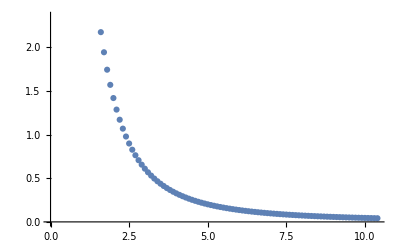

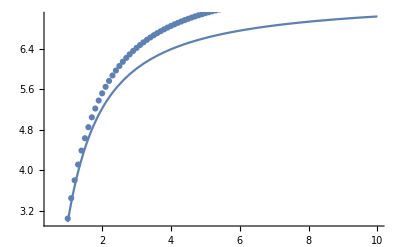

```mathematica
lambda=0.6;
sollambbeta={};
soldbetalambda={};
sols={};
GX[{X1_,X2_,X3_}] := lambda X1 X2- X3;
GRADX[{X1_,X2_,X3_}]:={lambda X2,lambda X1,-1};
(* Create Random Variables *)
RVVec={
ComputeRandomVarData["NORMAL",40.,5.]
,ComputeRandomVarData["NORMAL",50.,2.5]
,ComputeRandomVarData["NORMAL",1000.,200.]
};
RX=IdentityMatrix[Length[RVVec]];
steps=100;
betavec=Table[0,{steps}];
lambdavec=Table[0,{steps}];
dbetaL=0;
For[i=1,i<steps,i++,
sol=HRLF[GX,GRADX,RVVec,RX];
(*Nsamples=10000;
{post,randonSamples,failed,beta}=MonteCarlo[RVVec,Nsamples,RX,GX];*)
betavec[[i]]=sol[[4]];
lambdavec[[i]]=lambda;
If[i≠1,
dbetaL=(betavec[[i]]-betavec[[i-1]])/(lambdavec[[i]]-lambdavec[[i-1]]);
AppendTo[soldbetalambda,{lambda,dbetaL}];

];
AppendTo[sols,{lambda,sol[[4]]}];
lambda+=0.1;
];
betalamb[l_]:=(-1000+2000 l)/(√(40000+72500. l^2))
pll=Plot[betalamb[x],{x,0.5,10}];
pllll=ListPlot[sols];
plll=ListPlot[soldbetalambda]
Show[pll,pllll]
```

```mathematica
RIA[GX_,GRADX_,RVVec_,RX_,lambda0_,lambda1_,betatarget_]:=Block[{GXinternal,GRADXinternal,tol=10^-3,a,b,mu,lambda,erro,eps,sol,f1,f2,maxcounter=50,k=1},
eps=tol/10;
a=lambda0;
b=lambda1;
lambda=(a+b)*0.5-eps;
mu=(a+b)*0.5+eps;
erro =2*tol+1;
GXinternal[{X1_,X2_,X3_}] := GX[{X1,X2,X3,(a+b)*0.5}];
GRADXinternal[{X1_,X2_,X3_}]:=GRADX[{X1,X2,X3,(a+b)*0.5}];
sol=HRLF[GXinternal,GRADXinternal,RVVec,RX];
While[erro>tol && maxcounter>k,
If[sol[[4]]>betatarget,
b=mu;
lambda=(a+b)*0.5+eps;
mu=(a+b)*0.5-eps;
GXinternal[{X1_,X2_,X3_}] := GX[{X1,X2,X3,lambda}];
GRADXinternal[{X1_,X2_,X3_}]:=GRADX[{X1,X2,X3,lambda}];
sol=HRLF[GXinternal,GRADXinternal,RVVec,RX];
,
a=lambda;
lambda=(a+b)*0.5+eps;
mu=(a+b)*0.5-eps;
GXinternal[{X1_,X2_,X3_}] := GX[{X1,X2,X3,mu}];
GRADXinternal[{X1_,X2_,X3_}]:=GRADX[{X1,X2,X3,mu}];
sol=HRLF[GXinternal,GRADXinternal,RVVec,RX];


];
erro=Abs[sol[[4]]-betatarget];
AppendTo[sol,lambda];
AppendTo[sol,betatarget];
Print[TableForm[{{"X1","X2","X3","β","G(X)","lambda","βtarget"},sol}]];
(*Print["mu  = ",mu];
Print["lambda  = ",lambda];
Print["beta  = ",sol[[4]]];*)
k++;
];
Print["k  = ",k];
Print["Erro  = ",erro];
AppendTo[sol,lambda];
AppendTo[sol,betatarget];
sol
]
```

```mathematica
GX[{X1_,X2_,X3_,mult_}] := mult X1 X2- X3;
GRADX[{X1_,X2_,X3_,mult_}]:={mult X2,mult X1,-1};
```

```mathematica
sol=RIA[GX,GRADX,RVVec,RX,0,2,4]
(*Print[TableForm[{{"X1","X2","X3","β","G(X)","lambda","βtarget"},sol}]]*)
```

y = {0.,0.,0.}

grady = {250.,100.,-200.}

g = 1000.

y = {-2.22222,-0.888889,1.77778}

grady = {238.889,72.2222,-200.}

g = 24.6914

y = {-2.27788,-0.688661,1.90706}

grady = {241.392,71.5265,-200.}

g = -0.139299

y = {0.,0.,0.}

grady = {374.963,149.985,-200.}

g = 1999.7

y = {-3.69198,-1.47679,1.96925}

grady = {347.275,80.7673,-200.}

g = 102.22

y = {-3.94288,-0.917012,2.27075}

grady = {357.77,76.0634,-200.}

g = -2.63316

y = {-3.97721,-0.845572,2.22333}

grady = {359.11,75.4197,-200.}

g = -0.0459875

X1 | X2 | X3 | β | G(X) | lambda | βtarget
20.0894 | 47.9092 | 1443.56 | 4.63414 | -0.000851705 | 1.50005 | 4

y = {0.,0.,0.}

grady = {312.494,124.998,-200.}

g = 1499.95

y = {-3.05803,-1.22321,1.95718}

grady = {293.381,77.2167,-200.}

g = 58.4461

y = {-3.20302,-0.84302,2.18352}

grady = {299.322,74.9514,-200.}

g = -0.861266

y = {-3.22709,-0.808077,2.15627}

grady = {299.868,74.5752,-200.}

g = -0.0131457

X1 | X2 | X3 | β | G(X) | lambda | βtarget
23.8514 | 47.992 | 1430.82 | 3.96438 | -0.000199286 | 1.24998 | 4

y = {0.,0.,0.}

grady = {343.703,137.481,-200.}

g = 1749.63

y = {-3.39683,-1.35873,1.97661}

grady = {320.353,79.1061,-200.}

g = 79.3163

y = {-3.594,-0.887481,2.24377}

grady = {328.452,75.7178,-200.}

g = -1.59675

y = {-3.62379,-0.83539,2.20659}

grady = {329.347,75.2059,-200.}

g = -0.0266672

X1 | X2 | X3 | β | G(X) | lambda | βtarget
21.8622 | 47.9291 | 1440.58 | 4.32413 | -0.000456957 | 1.37501 | 4

y = {0.,0.,0.}

grady = {328.123,131.249,-200.}

g = 1624.99

y = {-3.23362,-1.29345,1.97098}

grady = {306.903,78.198,-200.}

g = 68.6192

y = {-3.40441,-0.867435,2.21856}

grady = {313.892,75.396,-200.}

g = -1.1937

y = {-3.43148,-0.824231,2.1864}

grady = {314.601,74.952,-200.}

g = -0.0191829

X1 | X2 | X3 | β | G(X) | lambda | βtarget
22.8266 | 47.9543 | 1436.7 | 4.15142 | -0.000311258 | 1.31249 | 4

y = {0.,0.,0.}

grady = {320.309,128.123,-200.}

g = 1562.47

y = {-3.14736,-1.25894,1.96521}

grady = {300.146,77.7171,-200.}

g = 63.4588

y = {-3.30515,-0.855805,2.20236}

grady = {306.603,75.1901,-200.}

g = -1.01874

y = {-3.33075,-0.81682,2.17268}

grady = {307.227,74.7801,-200.}

g = -0.0159825

X1 | X2 | X3 | β | G(X) | lambda | βtarget
23.3317 | 47.9714 | 1434.03 | 4.05971 | -0.000251117 | 1.28123 | 4

y = {0.,0.,0.}

grady = {316.401,126.56,-200.}

g = 1531.21

y = {-3.10309,-1.24123,1.96149}

grady = {296.765,77.4695,-200.}

g = 60.9335

y = {-3.25444,-0.849562,2.19328}

grady = {302.961,75.075,-200.}

g = -0.937854

y = {-3.27929,-0.812621,2.16483}

grady = {303.545,74.6819,-200.}

g = -0.0145192

X1 | X2 | X3 | β | G(X) | lambda | βtarget
23.5897 | 47.9813 | 1432.5 | 4.01251 | -0.000224187 | 1.2656 | 4

y = {0.,0.,0.}

grady = {314.447,125.779,-200.}

g = 1515.58

y = {-3.08066,-1.23226,1.95941}

grady = {295.073,77.3437,-200.}

g = 59.685

y = {-3.22882,-0.846329,2.18849}

grady = {301.141,75.0143,-200.}

g = -0.899027

y = {-3.25328,-0.810393,2.16064}

grady = {301.706,74.6296,-200.}

g = -0.0138213

X1 | X2 | X3 | β | G(X) | lambda | βtarget
23.7201 | 47.9865 | 1431.67 | 3.98856 | -0.000211486 | 1.25779 | 4

y = {0.,0.,0.}

grady = {315.374,126.15,-200.}

g = 1522.99

y = {-3.09132,-1.23653,1.96041}

grady = {295.876,77.4035,-200.}

g = 60.2761

y = {-3.241,-0.847872,2.19078}

grady = {302.004,75.0433,-200.}

g = -0.917314

y = {-3.26564,-0.811461,2.16265}

grady = {302.579,74.6547,-200.}

g = -0.0141496

X1 | X2 | X3 | β | G(X) | lambda | βtarget
23.6582 | 47.984 | 1432.07 | 3.99995 | -0.000217449 | 1.2617 | 4

k  = 9

Erro  = 0.0000512391

{23.6582,47.984,1432.07,3.99995,-0.000217449,1.2617,4,1.2617,4}

```mathematica
GX[{X1_,X2_,X3_,X4_,X5_,X6_,mult_}] :=mult X5-(6000*X1*X2)/(X3*X4^2);
GRADX[{X1_,X2_,X3_,X4_,X5_,X6_,mult_}]:={-(6000 X2)/(X3 X4^2),-(6000 X1)/(X3 X4^2),(6000 X1 X2)/(X3^2 X4^2),(12000 X1 X2)/(X3 X4^3),mult,0};
(* Create Random Variables *)
RVVec={
ComputeRandomVarData["NORMAL",100.,20.]
,ComputeRandomVarData["NORMAL",1000.,10.]
,ComputeRandomVarData["NORMAL",50.,5.]
,ComputeRandomVarData["NORMAL",200.,20.]
,ComputeRandomVarData["LOGNORMAL",500.,50.]
,ComputeRandomVarData["LOGNORMAL",70.,3.5]
};
RX=IdentityMatrix[Length[RVVec]];
RX[[5,6]]=RX[[6,5]]=0.5;
```

```mathematica
RIA[GX_,GRADX_,RVVec_,RX_,lambda0_,lambda1_,betatarget_]:=Block[{GXinternal,GRADXinternal,tol=10^-3,a,b,mu,lambda,erro,eps,sol,f1,f2,maxcounter=50,k=1},
eps=tol/10;
a=lambda0;
b=lambda1;
lambda=(a+b)*0.5-eps;
mu=(a+b)*0.5+eps;
erro =2*tol+1;
GXinternal[{X1_,X2_,X3_,X4_,X5_,X6_}] := GX[{X1,X2,X3,X4,X5,X6,(a+b)*0.5}];
GRADXinternal[{X1_,X2_,X3_,X4_,X5_,X6_}]:=GRADX[{X1,X2,X3,X4,X5,X6,(a+b)*0.5}];
sol=HRLF[GXinternal,GRADXinternal,RVVec,RX];
While[erro>tol && maxcounter>k,
If[sol[[4]]>betatarget,
b=mu;
lambda=(a+b)*0.5+eps;
mu=(a+b)*0.5-eps;
GXinternal[{X1_,X2_,X3_,X4_,X5_,X6_}] := GX[{X1,X2,X3,X4,X5,X6,lambda}];
GRADXinternal[{X1_,X2_,X3_,X4_,X5_,X6_}]:=GRADX[{X1,X2,X3,X4,X5,X6,lambda}];
sol=HRLF[GXinternal,GRADXinternal,RVVec,RX];
,
a=lambda;
lambda=(a+b)*0.5+eps;
mu=(a+b)*0.5-eps;
GXinternal[{X1_,X2_,X3_,X4_,X5_,X6_}] := GX[{X1,X2,X3,X4,X5,X6,mu}];
GRADXinternal[{X1_,X2_,X3_,X4_,X5_,X6_}]:=GRADX[{X1,X2,X3,X4,X5,X6,mu}];
sol=HRLF[GXinternal,GRADXinternal,RVVec,RX];


];
erro=Abs[sol[[4]]-betatarget];
AppendTo[sol,lambda];
AppendTo[sol,betatarget];
Print[TableForm[{{"X1","X2","X3","β","G(X)","lambda","βtarget"},sol}]];
(*Print["mu  = ",mu];
Print["lambda  = ",lambda];
Print["beta  = ",sol[[4]]];*)
k++;
];
Print["k  = ",k];
Print["Erro  = ",erro];
AppendTo[sol,lambda];
AppendTo[sol,betatarget];
sol
]
```

```mathematica
sol=RIA[GX,GRADX,RVVec,RX,0,10,4]
```

y = {0.,0.,0.,0.,0.0498757,0.0000537627}

grady = {-60.,-3.,30.,60.,249.378,0.}

g = 2200.

y = {1.86709,0.0933545,-0.933545,-1.86709,-15.0866,3.72281}

grady = {-100.144,-6.8706,75.8512,169.116,55.0964,0.}

g = -135.364

y = {2.67959,0.183838,-2.02957,-4.52507,-6.48773,2.56334}

grady = {-251.6,-19.2864,242.419,705.83,129.909,0.}

g = -629.852

y = {1.8062,0.138455,-1.7403,-5.06707,-2.06757,0.646465}

grady = {-298.935,-20.318,246.33,824.91,201.896,0.}

g = -10.6193

y = {1.90609,0.129553,-1.57066,-5.25983,-1.31621,0.0158342}

grady = {-317.199,-21.8777,259.879,924.274,217.609,0.}

g = -9.08759

y = {1.82403,0.125806,-1.49441,-5.31496,-1.25155,0.000110544}

grady = {-321.785,-21.9311,258.168,937.398,219.018,0.}

g = -0.238163

y = {0.,0.,0.,0.,0.0498757,0.0000537627}

grady = {-60.,-3.,30.,60.,124.697,0.}

g = 950.075

y = {2.39372,0.119686,-1.19686,-2.39372,-6.92337,0.926058}

grady = {-117.948,-8.71029,99.0638,229.303,62.1961,0.}

g = -248.56

y = {1.66506,0.122963,-1.39848,-3.23706,-2.19264,0.626447}

grady = {-152.7,-10.165,118.323,300.98,99.7024,0.}

g = -18.245

y = {1.76624,0.117576,-1.3686,-3.48135,-1.20366,0.0290992}

grady = {-163.782,-11.0689,128.39,340.005,110.04,0.}

g = -5.04533

y = {1.70093,0.114954,-1.33337,-3.53106,-1.14298,0.000105436}

grady = {-165.628,-11.0859,128.062,343.136,110.708,0.}

g = -0.023278

X1 | X2 | X3 | β | G(X) | lambda | βtarget
134.123 | 1001.14 | 43.4042 | 4.29631 | -0.00152646 | 2.50015 | 4

y = {0.,0.,0.,0.,0.0498757,0.0000537627}

grady = {-60.,-3.,30.,60.,62.3483,0.}

g = 325.037

y = {1.61013,0.0805067,-0.805067,-1.61013,-1.84073,0.0747009}

grady = {-92.7774,-6.12778,66.6966,146.193,51.6323,0.}

g = -95.6613

y = {1.09524,0.0723384,-0.787353,-1.72581,-0.679453,0.0317782}

grady = {-95.1985,-5.79838,62.9849,140.257,57.9735,0.}

g = 0.922562

y = {1.15158,0.0701409,-0.761905,-1.69664,-0.701308,-0.0000289316}

grady = {-94.2683,-5.79493,62.7726,139.678,57.8472,0.}

g = 0.0151252

X1 | X2 | X3 | β | G(X) | lambda | βtarget
122.928 | 1000.7 | 46.1831 | 2.29833 | 0.000152538 | 1.25007 | 4

y = {0.,0.,0.,0.,0.0498757,0.0000537627}

grady = {-60.,-3.,30.,60.,93.5125,0.}

g = 637.456

y = {2.25279,0.112639,-1.12639,-2.25279,-4.34934,0.386707}

grady = {-112.784,-8.1708,92.1836,211.173,60.2961,0.}

g = -213.537

y = {1.43307,0.103821,-1.17131,-2.68323,-1.2858,0.241624}

grady = {-127.077,-8.16648,92.5954,223.458,81.8477,0.}

g = 3.02126

y = {1.55958,0.100225,-1.1364,-2.74244,-1.00837,0.00210084}

grady = {-128.646,-8.43017,95.2053,232.547,84.1444,0.}

g = -0.320421

y = {1.52868,0.100174,-1.13131,-2.76332,-0.999878,1.90662×10^-6}

grady = {-129.315,-8.43409,95.1949,233.326,84.2157,0.}

g = 0.00216873

X1 | X2 | X3 | β | G(X) | lambda | βtarget
130.636 | 1001. | 44.3618 | 3.50178 | -1.92556×10^-6 | 1.87511 | 4

y = {0.,0.,0.,0.,0.0498757,0.0000537627}

grady = {-60.,-3.,30.,60.,109.1,0.}

g = 793.716

y = {2.36344,0.118172,-1.18172,-2.36344,-5.64985,0.633707}

grady = {-116.811,-8.59116,97.5396,225.267,61.7878,0.}

g = -240.713

y = {1.55127,0.114092,-1.29534,-2.99158,-1.70795,0.41774}

grady = {-140.493,-9.1936,105.737,262.658,91.5528,0.}

g = -2.59852

y = {1.67943,0.109899,-1.26397,-3.13977,-1.11245,0.0103294}

grady = {-146.096,-9.74765,111.702,284.491,97.156,0.}

g = -1.85434

y = {1.63042,0.108783,-1.2466,-3.17491,-1.0843,0.0000220788}

grady = {-147.309,-9.75661,111.582,286.215,97.4292,0.}

g = -0.00162

X1 | X2 | X3 | β | G(X) | lambda | βtarget
132.7 | 1001.08 | 43.8077 | 3.93443 | -0.000299766 | 2.18763 | 4

y = {0.,0.,0.,0.,0.0498757,0.0000537627}

grady = {-60.,-3.,30.,60.,116.893,0.}

g = 871.845

y = {2.38648,0.119324,-1.19324,-2.38648,-6.29127,0.774983}

grady = {-117.675,-8.68165,98.697,228.331,62.0985,0.}

g = -246.668

y = {1.60812,0.118642,-1.34878,-3.12033,-1.94375,0.518704}

grady = {-146.708,-9.68316,112.061,281.835,95.8125,0.}

g = -8.95131

y = {1.72644,0.11395,-1.31872,-3.31659,-1.15904,0.0181549}

grady = {-154.905,-10.4077,120.024,311.805,103.614,0.}

g = -3.23904

y = {1.66877,0.112121,-1.293,-3.35904,-1.11631,0.0000517095}

grady = {-156.425,-10.42,119.808,314.161,104.056,0.}

g = -0.00896123

X1 | X2 | X3 | β | G(X) | lambda | βtarget
133.476 | 1001.11 | 43.59 | 4.12288 | -0.000737296 | 2.34389 | 4

y = {0.,0.,0.,0.,0.0498757,0.0000537627}

grady = {-60.,-3.,30.,60.,113.006,0.}

g = 832.88

y = {2.3772,0.11886,-1.1886,-2.3772,-5.97248,0.703221}

grady = {-117.326,-8.64509,98.2292,227.092,61.9734,0.}

g = -244.257

y = {1.57982,0.116408,-1.32268,-3.05784,-1.82438,0.467434}

grady = {-143.642,-9.44039,108.92,272.289,93.7362,0.}

g = -5.43998

y = {1.70395,0.111987,-1.29207,-3.23003,-1.13612,0.0138901}

grady = {-150.504,-10.0785,115.868,298.073,100.398,0.}

g = -2.4944

y = {1.65051,0.110526,-1.27068,-3.26884,-1.10108,0.0000345253}

grady = {-151.869,-10.0889,115.703,300.099,100.749,0.}

g = -0.004618

X1 | X2 | X3 | β | G(X) | lambda | βtarget
133.107 | 1001.1 | 43.6943 | 4.03094 | -0.000483928 | 2.26576 | 4

y = {0.,0.,0.,0.,0.0498757,0.0000537627}

grady = {-60.,-3.,30.,60.,111.058,0.}

g = 813.348

y = {2.37093,0.118546,-1.18546,-2.37093,-5.81183,0.668211}

grady = {-117.091,-8.62045,97.9141,226.257,61.8888,0.}

g = -242.637

y = {1.5656,0.115263,-1.30919,-3.02525,-1.76585,0.442408}

grady = {-142.081,-9.3177,107.337,267.492,92.6595,0.}

g = -3.93987

y = {1.69197,0.11096,-1.27823,-3.18544,-1.12441,0.0120269}

grady = {-148.304,-9.91345,113.789,291.272,98.7821,0.}

g = -2.16157

y = {1.64072,0.109675,-1.25888,-3.22241,-1.0929,0.0000277811}

grady = {-149.593,-9.92315,113.647,293.144,99.093,0.}

g = -0.00297202

X1 | X2 | X3 | β | G(X) | lambda | βtarget
132.909 | 1001.09 | 43.7497 | 3.98334 | -0.000384223 | 2.2267 | 4

y = {0.,0.,0.,0.,0.0498757,0.0000537627}

grady = {-60.,-3.,30.,60.,112.022,0.}

g = 823.014

y = {2.37417,0.118709,-1.18709,-2.37417,-5.8914,0.685454}

grady = {-117.212,-8.63319,98.077,226.689,61.9326,0.}

g = -243.474

y = {1.57264,0.115832,-1.3159,-3.04149,-1.7947,0.454734}

grady = {-142.855,-9.37851,108.122,269.867,93.1953,0.}

g = -4.66118

y = {1.69796,0.111472,-1.28512,-3.20761,-1.13022,0.0129267}

grady = {-149.392,-9.9951,114.818,294.631,99.5819,0.}

g = -2.32289

y = {1.64562,0.1101,-1.26477,-3.24549,-1.09699,0.000030977}

grady = {-150.719,-10.0052,114.664,296.578,99.9125,0.}

g = -0.00374664

X1 | X2 | X3 | β | G(X) | lambda | βtarget
133.008 | 1001.1 | 43.722 | 4.00702 | -0.000431494 | 2.24623 | 4

y = {0.,0.,0.,0.,0.0498757,0.0000537627}

grady = {-60.,-3.,30.,60.,111.545,0.}

g = 818.231

y = {2.3726,0.11863,-1.1863,-2.3726,-5.85204,0.676901}

grady = {-117.153,-8.62703,97.9981,226.48,61.9114,0.}

g = -243.069

y = {1.56916,0.115551,-1.31259,-3.03348,-1.7804,0.44862}

grady = {-142.473,-9.34845,107.734,268.692,92.9309,0.}

g = -4.29915

y = {1.69501,0.11122,-1.28172,-3.19666,-1.12735,0.0124761}

grady = {-148.854,-9.95469,114.309,292.967,99.1862,0.}

g = -2.24223

y = {1.64321,0.109891,-1.26187,-3.2341,-1.09498,0.0000293619}

grady = {-150.161,-9.96459,114.161,294.877,99.507,0.}

g = -0.00335386

X1 | X2 | X3 | β | G(X) | lambda | βtarget
132.959 | 1001.09 | 43.7356 | 3.99534 | -0.00040761 | 2.23646 | 4

y = {0.,0.,0.,0.,0.0498757,0.0000537627}

grady = {-60.,-3.,30.,60.,111.779,0.}

g = 820.573

y = {2.37338,0.118669,-1.18669,-2.37338,-5.87132,0.681083}

grady = {-117.183,-8.63008,98.0372,226.583,61.9219,0.}

g = -243.27

y = {1.57086,0.115689,-1.31421,-3.03741,-1.78739,0.45161}

grady = {-142.66,-9.36317,107.924,269.268,93.0605,0.}

g = -4.47513

y = {1.69646,0.111343,-1.28339,-3.20203,-1.12876,0.0126954}

grady = {-149.117,-9.97447,114.558,293.781,99.3799,0.}

g = -2.28151

y = {1.6444,0.109994,-1.26329,-3.23968,-1.09597,0.0000301443}

grady = {-150.434,-9.98446,114.407,295.709,99.7055,0.}

g = -0.00354379

X1 | X2 | X3 | β | G(X) | lambda | βtarget
132.983 | 1001.09 | 43.7289 | 4.00107 | -0.00041918 | 2.24135 | 4

y = {0.,0.,0.,0.,0.0498757,0.0000537627}

grady = {-60.,-3.,30.,60.,111.667,0.}

g = 819.452

y = {2.37301,0.118651,-1.18651,-2.37301,-5.86209,0.67908}

grady = {-117.169,-8.62863,98.0186,226.534,61.9169,0.}

g = -243.174

y = {1.57005,0.115623,-1.31344,-3.03553,-1.78404,0.450178}

grady = {-142.57,-9.35612,107.833,268.992,92.9985,0.}

g = -4.3906

y = {1.69577,0.111284,-1.28259,-3.19946,-1.12808,0.0125901}

grady = {-148.991,-9.96501,114.439,293.391,99.2872,0.}

g = -2.26266

y = {1.64383,0.109945,-1.26261,-3.23701,-1.0955,0.0000297678}

grady = {-150.304,-9.97495,114.289,295.311,99.6105,0.}

g = -0.00345232

X1 | X2 | X3 | β | G(X) | lambda | βtarget
132.972 | 1001.09 | 43.7321 | 3.99832 | -0.000413613 | 2.2389 | 4

y = {0.,0.,0.,0.,0.0498757,0.0000537627}

grady = {-60.,-3.,30.,60.,111.718,0.}

g = 819.962

y = {2.37318,0.118659,-1.18659,-2.37318,-5.86629,0.679992}

grady = {-117.175,-8.62929,98.0271,226.556,61.9192,0.}

g = -243.218

y = {1.57042,0.115653,-1.31379,-3.03639,-1.78557,0.45083}

grady = {-142.611,-9.35933,107.874,269.118,93.0268,0.}

g = -4.42902

y = {1.69608,0.111311,-1.28295,-3.20063,-1.12839,0.012638}

grady = {-149.049,-9.96932,114.493,293.569,99.3294,0.}

g = -2.27124

y = {1.64409,0.109967,-1.26292,-3.23823,-1.09571,0.0000299388}

grady = {-150.363,-9.97928,114.343,295.492,99.6538,0.}

g = -0.00349385

X1 | X2 | X3 | β | G(X) | lambda | βtarget
132.977 | 1001.09 | 43.7307 | 3.99957 | -0.000416141 | 2.24012 | 4

k  = 13

Erro  = 0.000426599

{132.977,1001.09,43.7307,3.99957,-0.000416141,2.24012,4,2.24012,4}

```mathematica
GX[{X1_,X2_,X3_,X4_,X5_,X6_,mult_}] :=mult X5-(6000*X1*X2)/(X3*X4^2);
GRADX[{X1_,X2_,X3_,X4_,X5_,X6_,mult_}]:={-(6000 X2)/(X3 X4^2),-(6000 X1)/(X3 X4^2),(6000 X1 X2)/(X3^2 X4^2),(12000 X1 X2)/(X3 X4^3),mult,0};
(* Create Random Variables *)
RVVec={
ComputeRandomVarData["NORMAL",100.,20.]
,ComputeRandomVarData["NORMAL",1000.,10.]
,ComputeRandomVarData["NORMAL",50.,5.]
,ComputeRandomVarData["NORMAL",200.,20.]
,ComputeRandomVarData["LOGNORMAL",500.,50.]
,ComputeRandomVarData["LOGNORMAL",70.,3.5]
};
RX=IdentityMatrix[Length[RVVec]];
RX[[5,6]]=RX[[6,5]]=0.5;
```

```mathematica
D[mult X1-X2/(X3 X4),X4]
```

X2/(X3 X4^2)

```mathematica
172 0.15
```

25.8

```mathematica
68950 0.1
```

6895.

```mathematica
20 0.3
```

6.

```mathematica
e= 2 10^8;
A=1.5 10^-3;
free=1;
zero=0.;
b=0.01;
h=0.015;
FandPrescribedU={{1,{{0,-20},{0,0},{zero,free}}},{2,{{-20,-45},{0,0},{free,free}}},{3,{{0,0},{0,0},{zero,zero}}}}
els={{1,2,{{0,0},{2,0}},{e,b,h,2}},{2,3,{{2,0},{0,1.5}},{e,b,h,Sqrt[1.5 1.5+2 2]}},{3,1,{{0,1.5}, {0,0}},{e,b,h,1.5}}};
sol=Assemble[els,3,FandPrescribedU];
```

{{1,{{0,-20},{0,0},{0.,1}}},{2,{{-20,-45},{0,0},{1,1}}},{3,{{0,0},{0,0},{0.,0.}}}}

```mathematica
D[mult X1-X2/b h,X2]
```

-1.5

```mathematica
els[[1,4,4]]
```

2

```mathematica
MonteCarlo[RvVec_,Nsamples_,RX_,lambda_]:=Block[{y,z,x,counter,Pf,beta,i,PostProc,xfailed={},fx,hx,vartemp,inercia,k,L,sol,e,b,h,f1,f2,free,zero,els,FandPrescribedU},

y=ComputeY[RvVec,Nsamples];
z=FromYtoZ[y,RX];
{x,fx,hx}=FromZtoX[RvVec,z];

PostProc=Table[0,{Nsamples},{2}];

counter=0;
vartemp=0;
For[i=1,i≤Nsamples,i++,
e= x[[i,1]];
free=1;
zero=0.;
b=x[[i,2]] ;
h=x[[i,3]]lambda;
f1=x[[i,4]];
f2=x[[i,5]];
(*Print["b = ",b];
Print["h= ",h];
Print["f1 = ",f1];
Print["f2 = ",f2];
Print["e = ",e];*)
FandPrescribedU={{1,{{0,f1},{0,0},{zero,free}}},{2,{{f1,f2},{0,0},{free,free}}},{3,{{0,0},{0,0},{zero,zero}}}};
els={{1,2,{{0,0},{2,0}},{e,b,h,2}},{2,3,{{2,0},{0,1.5}},{e,b,h,Sqrt[1.5 1.5+2 2]}},{3,1,{{0,1.5}, {0,0}},{e,b,h,1.5}}};
sol=Assemble[els,3,FandPrescribedU];
(*Print["sol = ",sol];
Print["sample = ",i];*)
For[k=1,k≤Length[sol],k++,
(*Print["barra = ",k];*)
(*Print["x[[i,6]]-Abs[sol[[k]]/(b h)] = ",x[[i,6]]-Abs[sol[[k]]/(b h)]];*)
inercia=(b h^3)/12;
L=els[[1,4,4]];


(*Print["carga crítica= ",(Pi^2  e inercia)/L^2];
Print["inercia= ",inercia];
Print["forca de atuante= ",sol[[k]]];
Print["forca resistente= ",x[[i,6]] b h];*)
If[sol[[k]]<0 && (Abs[sol[[k]]]-(Pi^2  e inercia)/L^2)>0,

(*Print["Falha por flambagem / carga crítica= ",(Pi^2  e inercia)/L^2];
Print["Falha por flambagem / carga atuante= ",sol[[k]]];*)
AppendTo[xfailed,x[[i]]];
counter++;
Break[];
];
If[x[[i,6]]-Abs[sol[[k]]/(b h)]≤10^-8,

(*Print["Falha por escoamento / tensao de escoamento= ",x[[i,6]]];
Print["Falha por escoamento / tensao de atuante= ",sol[[k]]];*)
AppendTo[xfailed,x[[i]]];
counter++;

Break[];
];

PostProc[[i,1]]=i;
beta=-InvPHI[N[counter/Nsamples]];
PostProc[[i,2]]=beta;
];

(*Print["Counter = ",counter];*)
Pf=N[counter/Nsamples];
(*Print["Pf Crude Monte Carlo  = ",Pf];
Print["β Crude Monte Carlo = ",beta];*)
];
{PostProc,x,xfailed,beta}
];
```

```mathematica
RVVec={
ComputeRandomVarData["NORMAL",2. 10^8,200000](*E*),
ComputeRandomVarData["NORMAL",0.05,0.01],(*b*)
ComputeRandomVarData["NORMAL",0.025,0.0025],(*h*)
ComputeRandomVarData["NORMAL",-5,2],(*f1*)
ComputeRandomVarData["NORMAL",-10,4.5],(*f2*)
ComputeRandomVarData["NORMAL",210000,2100](*sigmay*)
};
RX=IdentityMatrix[Length[RVVec]];
```

```mathematica
{PostProc2,x,xfailed,beta}=MonteCarlo[RVVec,1000,RX];
```

Set::shape: Lists {PostProc2,x,xfailed,beta} and MonteCarlo[{{2.×10^8,200000,2.×10^8,200000,1},{0.05,0.01,0.05,0.01,1},{0.025,0.0025,0.025,0.0025,1},{-5,2,-5,2,1},{-10,4.5,-10,4.5,1},{210000,2100,210000,2100,1}},1000,{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}] are not the same shape.

```mathematica
beta
```

beta

```mathematica
ListPlot[PostProc2,PlotRange->Automatic]
```

ListPlot::lpn: PostProc2 is not a list of numbers or pairs of numbers.

ListPlot[PostProc2,PlotRange→Automatic]

## -Graphics-

## -Graphics-

```mathematica
(Pi^2 e (b h^3/12))/3.05^2
(Pi^2 e (b h^3/12))/4.31^2
```

0.596791

0.29886

```mathematica
0.265 0.265
```

0.070225

```mathematica
e= 68950;
free=1;
zero=0.;
b=0.265 ;
h=0.265;
f1=20;
f2=-15;
(*Print["b = ",b];
Print["h= ",h];
Print["f1 = ",f1];
Print["f2 = ",f2];
Print["e = ",e];*)
FandPrescribedU={{1,{{0,0},{0,0},{zero,zero}}},{2,{{0,0},{0,0},{free,zero}}},{3,{{0,f2},{0,0},{free,free}}},{4,{{f1,f2},{0,0},{free,free}}}};
els={{1,4,{{0,0},{0,3.05}},{e,b,h,3.05}},{4,3,{{0,3.05},{3.05,3.05}},{e,b,h,3.05}},{3,2,{{3.05,3.05}, {3.05,0}},{e,b,h,3.05}},{1,3,{{0,0},{3.05,3.05}},{e,b,h,4.31}},{4,2,{{3.05,0},{0,3.05}},{e,b,h,4.31}}};
sol=Assemble[els,4,FandPrescribedU]
```

{-15.,-20.,-35.,28.2843,7.10543×10^-15}

```mathematica
RVVec={
ComputeRandomVarData["NORMAL",172,0.15](*sigy*),
ComputeRandomVarData["NORMAL",68950,0.1],(*E*)
ComputeRandomVarData["NORMAL",20,6],(*fx*)
ComputeRandomVarData["NORMAL",-15,3](*fy*)
};
RX=IdentityMatrix[Length[RVVec]];
```

0

0

```mathematica
els[[2]][[3]][[2]][[1]]
```

3.05

```mathematica
GX1[{X1_,X2_,X3_,X4_},mult_] :=Block[{G1,G2},
els={{1,4,{{0,0},{0,3.05}},{e,b,h,3.05}},{4,3,{{0,3.05},{3.05,3.05}},{e,b,h,3.05}},{3,2,{{3.05,3.05}, {3.05,0}},{e,b,h,3.05}},{1,3,{{0,0},{3.05,3.05}},{e,b,h,4.31}},{4,2,{{3.05,0},{0,3.05}},{e,b,h,4.31}}};
sol=Assemble[els,4,{{1,{{0,0},{0,0},{zero,zero}}},{2,{{0,0},{0,0},{free,zero}}},{3,{{0,X4},{0,0},{free,free}}},{4,{{X3,X4},{0,0},{free,free}}}}];
G1=X1-Abs[sol];
G1
];
```

```mathematica
GX2[{X1_,X2_,X3_,X4_},mult_,bar_] :=Block[{G1,G2,x1,x0,y0,y1,L},
els={{1,4,{{0,0},{0,3.05}},{e,b,h,3.05}},{4,3,{{0,3.05},{3.05,3.05}},{e,b,h,3.05}},{3,2,{{3.05,3.05}, {3.05,0}},{e,b,h,3.05}},{1,3,{{0,0},{3.05,3.05}},{e,b,h,4.31}},{4,2,{{3.05,0},{0,3.05}},{e,b,h,4.31}}};
sol=Assemble[els,4,{{1,{{0,0},{0,0},{zero,zero}}},{2,{{0,0},{0,0},{free,zero}}},{3,{{0,X4},{0,0},{free,free}}},{4,{{X3,X4},{0,0},{free,free}}}}];
x0=els[[bar]][[3]][[1]][[1]];
y0=els[[bar]][[3]][[1]][[2]];
x1=els[[bar]][[3]][[2]][[1]];
y1=els[[bar]][[3]][[2]][[2]];
L=Sqrt[(x1-x0)^2 + (y1-y0)^2];
G2=Pi^2 X2 ((b h^3)/12)/L^2-mult Abs[sol[[bar]]];
G2
];
```

```mathematica
sol
```

{-14.9982,-20.,-34.9982,28.2843,0.}

```mathematica
GXX[{X1_,X2_,X3_,X4_}]:=Block[{},
Return[{GX1[{X1,X2,X3,X4}],GX2[{X1,X2,X3,X4}]}]
]
```

```mathematica
GXX[{172,68950,20,-15}][[1]]
```

{157.,152.,137.,143.716,172.}

```mathematica
GX1[{172,68950,20,-15}]
```

{157.,152.,137.,143.716,172.}

```mathematica
GX[{172,68,950,20,-15}]
```

GX[{172,68,950,20,-15}]

```mathematica
ComputeGrad[GX2,{172,89950,20,-15},5]
```

{{0.,0.000436016,0.,1.},{0.,0.000436016,-1.,7.10543×10^-12},{0.,0.000436016,-1.,1.},{0.,0.000218008,-1.41421,0.},{0.,0.000218008,3.55271×10^-12,3.55271×10^-12}}

```mathematica
ComputeGrad[fx_,pt_,nfuncs_]:=Block[{nvar,x0,x1,y0,y1,dy,dx,dydx,i,steps=10,j,x,k,xn1,xn,eps=0.001,funcappend,Sol,var=0},
nvar=Length[pt];
Sol=Table[0,{nfuncs},{nvar}];

For[k=1,k≤nfuncs,k++,
For[i=1,i≤nvar,i++,
x0=pt[[i]]-eps;
x1=pt[[i]]+eps;

xn1=pt;
xn=pt;
x=pt;
dx=(x1-x0)/steps;
xn1[[i]]+=dx;
var=0;
For[j=1,j<=steps,j++,
var+=(fx[xn1,1,k]-fx[xn,1,k])/dx;
xn=xn1;
xn1=xn;
xn1[[i]]+=dx;
];
var/=steps;

Sol[[k,i]]=var;
];

];
Sol
]
```

```mathematica
FF[{x_,y_}]:={2 x^3 - 3x y^2,2 x^3 y-3y, 3 x y^2- y y}
ComputeGrad[FF,{1,2},3]
D[FF[{x,y}],x]/.x->1/.y->2
```

{{-5.98799,-12.006},{12.024,-1.},{12.,8.004}}

{-6,12,12}

```mathematica
Transpose[RVVec]
```

{{172,68950,20,-15},{0.15,0.1,6,3},{172,68950,20,-15},{0.15,0.1,6,3},{1,1,1,1}}

```mathematica
HRLF[RvVec_,Rx_,lambda_]:=Block[{barss={},nlsf,lsf,bars,bar,i,y0,Mneq,x,y,g,gradx,grady,betan,betan1,k,checkconv=1,tol=10^-3,NmaxIT=200,Jyz,Jzy,Jzx,Jxz,Jxy,Jyx,alpha,xn,xmax,xmin,nrv,PostProcess={},post=True,Sdev,DistribCases,Mean},
k=1;
Mean=Transpose[RvVec][[1]];
x=Mean;
Sdev=Transpose[RvVec][[2]];
DistribCases=Transpose[RvVec][[5]];
nrv=Length[RvVec];
xmax=Table[0,{nrv}];
xmin=Table[0,{nrv}];
For[i=1,i≤nrv,i++,
{xmax[[i]],xmin[[i]]}=ComputeExtremes[RvVec[[i]]];
];
{Jzy,Jyz}  = ComputeJYZ[Rx];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
(*For[lsf=1,lsf≤nlsf,lsf++,*)
(*bars=Length[GX[x][[lsf]]];*)
For[bar=1,bar≤5,bar++,
g=GX2[x,lambda,bar];

k=1;
betan=0;
While[checkconv>tol &&k< NmaxIT,
(*Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",N[g], "  | y = ",y ];*)
Gradx=ComputeGrad[GX2,x,5];
grady=Transpose[Jxy].Gradx[[bar]];
y=((grady.y)-g)/(grady.grady)grady;
x=Jxy.y+Mneq;
(*Print["*****"];
xn=Jxy.y+Mneq;
Print["xmin = ",xmin, " xmax = ",xmax, " x = ",x , " xn = ",xn];
x=PenalizeXhalf[x,xn,xmin,xmax];
Print["xmin = ",xmin, " xmax = ",xmax, " x = ",x , " xn = ",xn];*)
If[post==True,
AppendTo[PostProcess,x];
];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
g=GX2[x,lambda,bar];
betan1=Norm[y];
checkconv=Abs[betan1-betan];
betan=betan1;
k++;
];
Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",N[g], "  | x = ",x ," | β = ",betan];
checkconv=1.;
k=1.;
AppendTo[barss,{x[[1]],x[[2]],x[[3]],x[[4]],betan,g}];
alpha=( grady/(√(grady.grady)))^2;
];

(*Print[" SOLUTION "];
Print[" x = ",x];
Print[" β = ",betan];
Print[ " Pf = ",PHI[-betan] ];*)
(*Print[TableForm[{{"X"," β ", "PF", "Y "," α "},{x,betan,PHI[-betan] ,y,alpha}}]];*)
(*Print[TableForm[{{" X1 "," X2 ", " X3 ", " PF "," β "},{x[[1]],x[[2]],x[[3]],PHI[-betan],betan}}]];*)
barss
];
```

```mathematica
sol=HRLF[RVVec,RX,1.1]
```

| iter = 6  | residual = 0.00045211 | G(x) = -0.000135633  | x = {172.,68950.,20.,-27.3304} | β = 4.11013

| iter = 6  | residual = 0.000134388 | G(x) = -0.000080633  | x = {172.,68950.,27.3303,-15.} | β = 1.22172

| iter = 6  | residual = 0.000245969 | G(x) = 0.000165001  | x = {172.,68950.,13.8641,-13.466} | β = 1.14336

| iter = 5  | residual = 0.000770254 | G(x) = -0.000653582  | x = {172.,68950.,9.66313,-15.} | β = 1.72281

| iter = 4  | residual = 4.12459×10^-7 | G(x) = -1.09884×10^-14  | x = {172.,-1.45519×10^-11,20.,-15.} | β = 689500.

{{172.,68950.,20.,-27.3304,4.11013,-0.000135633},{172.,68950.,27.3303,-15.,1.22172,-0.000080633},{172.,68950.,13.8641,-13.466,1.14336,0.000165001},{172.,68950.,9.66313,-15.,1.72281,-0.000653582},{172.,-1.45519×10^-11,20.,-15.,689500.,-1.09884×10^-14}}

```mathematica
Length[sol]
```

5

```mathematica
sol[[2]][[5]]
```

1.67722

```mathematica
RIA[RVVec_,RX_,lambda0_,lambda1_,betatarget_]:=Block[{i,GXinternal,GRADXinternal,tol=10^-3,a,b,mu,lambda,erro,eps,sol,f1,f2,maxcounter=50,k=1},
eps=tol/10;
a=lambda0;
b=lambda1;
lambda=(a+b)*0.5-eps;
mu=(a+b)*0.5+eps;
erro =2*tol+1;
For[i=1,i≤Length[sol],i++,
sol=HRLF[RVVec,RX,lambda];
Print[sol];
While[erro>tol && maxcounter>k,
If[sol[[i]][[5]]>betatarget,
b=mu;
lambda=(a+b)*0.5+eps;
mu=(a+b)*0.5-eps;
sol=HRLF[RVVec,RX,lambda];
,
a=lambda;
lambda=(a+b)*0.5+eps;
mu=(a+b)*0.5-eps;
sol=HRLF[RVVec,RX,lambda];
];
erro=Abs[sol[[i]][[5]]-betatarget];
AppendTo[sol,lambda];
AppendTo[sol,betatarget];
Print[TableForm[{{"X1","X2","X3","X4","β","G(X)","lambda","βtarget"},{sol[[i]][[1]],sol[[i]][[2]],sol[[i]][[3]],sol[[i]][[4]],sol[[i]][[5]],lambda,betatarget}}]];
(*Print["mu  = ",mu];
Print["lambda  = ",lambda];
Print["beta  = ",sol[[4]]];*)
k++;
];
];
Print["k  = ",k];
Print["Erro  = ",erro];
sol
]
```

```mathematica
sol=RIA[RVVec,RX,0,10,4]
```

k  = 1

Erro  = 501/500

{{172.,68950.,20.,-27.3304,4.11013,-0.000135633},{172.,68950.,27.3303,-15.,1.22172,-0.000080633},{172.,68950.,13.8641,-13.466,1.14336,0.000165001},{172.,68950.,9.66313,-15.,1.72281,-0.000653582},{172.,-1.45519×10^-11,20.,-15.,689500.,-1.09884×10^-14}}

```mathematica
RIA[RVVec_,RX_,lambda0_,lambda1_,betatarget_]:=Block[{GXinternal,GRADXinternal,tol=10^-3,a,b,mu,lambda,erro,eps,sol,f1,f2,maxcounter=50,k=1},
eps=tol/10;
a=lambda0;
b=lambda1;
lambda=(a+b)*0.5-eps;
mu=(a+b)*0.5+eps;
erro =2*tol+1;
Print["lambda  = ",lambda];
sol=MonteCarlo[RVVec,1000,RX,lambda];
While[erro>tol && maxcounter>k,
If[sol[[4]]>betatarget,
b=mu;
lambda=(a+b)*0.5+eps;
mu=(a+b)*0.5-eps;
sol=MonteCarlo[RVVec,1000,RX,lambda];
,
a=lambda;
lambda=(a+b)*0.5+eps;
mu=(a+b)*0.5-eps;
sol=MonteCarlo[RVVec,1000,RX,mu];
];
erro=Abs[sol[[4]]-betatarget];
Print["sol[[4]]  = ",sol[[4]]];
(*AppendTo[sol,lambda];
AppendTo[sol,betatarget];*)
(*Print[TableForm[{{"X1","X2","X3","X4","X5","X6","β","βtarget","lambda"},{sol[[2,1]],sol[[2,2]],sol[[2,3]],sol[[2,4]],sol[[2,5]],sol[[2,6]]},sol[[4]],betatarget,lambda}]];*)
(*Print["mu  = ",mu];
Print["betatarget  = ",betatarget];
Print["lambda  = ",lambda];*)
Print["beta  = ",sol[[4]]];
(*Print["mu  = ",mu];
Print["lambda  = ",lambda];
Print["beta  = ",sol[[4]]];*)
k++;
];
Print["k  = ",k];
Print["Erro  = ",erro];
(*AppendTo[sol,lambda];
AppendTo[sol,betatarget];
sol*)
]
```

```mathematica
(*RIA[RVVec,RX,0,2,1.03]*)
```

lambda  = 0.9999

Part::partw: Part 5 of {172.141,68950.1,26.4361,-16.2614} does not exist.

Part::partw: Part 6 of {172.141,68950.1,26.4361,-16.2614} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

sol[[4]]  = ∞

beta  = ∞

$Aborted